# Efficiency Comparison Physics Data

## Methods

```mathematica
(*Set directory paths.*)
SetDirectory[NotebookDirectory[]];
paretoEffsDir="pareto_effs";
```

```mathematica
strategyOrder={"cvar25","stability","cap","wasserstein","consistency"};
boxStrategyOrder={"cvar25","stability","cap","wasserstein","consistency"};
strategyMaximizeQ=<|"cvar25"->True,"cvar10"->True,"cap"->True,"stability"->False,"wasserstein"->False,"consistency"->True|>;
strategyStudyObj=<|"cvar25"->"cvar25eff","cvar10"->"cvar10eff","cap"->"cap","stability"->"drift","wasserstein"->"wasserstein","consistency"->"consistency"|>;
strategyPretty=<|"cvar25"->"semi-supervised","cvar10"->"semi-sup (CVaR10)","cap"->"CAP","stability"->"stable","wasserstein"->"wasserstein","consistency"->"consistency"|>;
strategyBoxColors=<|"cvar25"->"#3f90da","stability"->"#ffa90e","cap"->"#bd1f01","wasserstein"->"#832db6","consistency"->"#94a4a2"|>;
```

```mathematica
(*Background/reference datasets excluded from the signal mean. No bare "shifted": robustad signals are shifted_anomaly_*,its background shifted_normal_all is caught via "normal".*)
bkgDatasetQ[ds_String]:=StringContainsQ[ds,"normal"|"SingleNeutrino"|"ZB_"|"reference"];
numOrMissing[x_]:=If[NumericQ[x],N[x],Missing["NA"]];
```

```mathematica
(*Domain configuration for the model-picking analysis.*)
rebuttalDomain="physics";
rebuttalFrontsDir="paretos/physics";
rebuttalOutDir="effs/";
rebuttalTierSuffix="_250Hz";
rebuttalModelExps=<|"AE"->"physics_ae_pareto","VAE"->"physics_vae_pareto","DSAE"->"physics_dsae_pareto","DSVAE"->"physics_dsvae_pareto","SVDD"->"physics_svdd_pareto","RealNVP"->"physics_realnvp_pareto","DTE"->"physics_dte_pareto"|>;
```

## Data Import

```mathematica
strategyContextQ[strat_String,ctx_String]:=StringStartsQ[ctx,"summary/eff/"]&&With[{m=StringDrop[ctx,StringLength["summary/eff/"]]},Switch[strat,"cvar25",m==="cvar25_ema/max","cvar10",m==="cvar10_ema/max","cap",StringStartsQ[m,"cap_ema"]&&StringEndsQ[m,"/max"],"consistency",StringStartsQ[m,"consistency_ema"]&&StringEndsQ[m,"/max"],"stability",StringContainsQ[m,"drift_ema"]&&StringEndsQ[m,"/min"],"wasserstein",StringContainsQ[m,"w1dist_ema"]&&StringEndsQ[m,"/min"],_,False]];

(*Per-signal eval columns:eff_<label>_<dataset>,excluding the eff_med_/eff_min_ summaries;the plain eff_<label>scalar is the shortest prefix.*)
perSignalCols[hdr_List]:=Module[{eff,base,cols},eff=Select[hdr,StringQ[#]&&StringStartsQ[#,"eff_"]&&!StringStartsQ[#,"eff_med_"]&&!StringStartsQ[#,"eff_min_"]&];
base=SelectFirst[SortBy[eff,StringLength],Function[b,Count[eff,c_/;StringStartsQ[c,b<>"_"]]>=3]];
cols=Select[eff,StringStartsQ[#,base<>"_"]&];
<|"cols"->cols,"names"->(StringDrop[#,StringLength[base]+1]&/@cols)|>];

(*One record per run:strategy,Q' (optimized_main),Q'' (optimized_sec),per-signal TEST efficiencies at the run's own strategy checkpoint,and their mean over signal datasets.*)
loadRuns[exp_String]:=Module[{raw,hdr,idx,rows,runs=<||>,eraw,ehdr,eidx,erows,ps,rn,strat,arr,sig},raw=Import[FileNameJoin[{paretoEffsDir,exp<>".csv"}],"CSV"];
hdr=First[raw];rows=Rest[raw];
idx=AssociationThread[hdr->Range[Length[hdr]]];
Do[If[row[[idx["ckpt"]]]==="strategy",runs[row[[idx["run_name"]]]]=<|"strategy"->row[[idx["strategy"]]],"q0"->numOrMissing[row[[idx["optimized_main"]]]],"q1"->numOrMissing[row[[idx["optimized_sec"]]]]|>],{row,rows}];
eraw=Import[FileNameJoin[{paretoEffsDir,exp<>"_eval.csv"}],"CSV"];
ehdr=First[eraw];erows=Rest[eraw];
eidx=AssociationThread[ehdr->Range[Length[ehdr]]];
ps=perSignalCols[ehdr];
Do[rn=row[[eidx["run_name"]]];
If[KeyExistsQ[runs,rn]&&row[[eidx["split"]]]==="test"&&strategyContextQ[runs[rn]["strategy"],row[[eidx["context"]]]],arr=AssociationThread[ps["names"]->(numOrMissing[row[[eidx[#]]]]&/@ps["cols"])];
sig=DeleteMissing[KeySelect[arr,!bkgDatasetQ[#]&]];
If[Length[sig]>0,runs[rn]=Join[runs[rn],<|"testArr"->sig,"eff"->Mean[Values[sig]]|>]]],{row,erows}];
runs];

frontsOf[runs_Association]:=GroupBy[runs,#["strategy"]&];
```

```mathematica
(* q99 retraining campaigns: experiment map. Both the history and the
   _eval.csv harvests exist, so the standard loadRuns/rebuttalRuns/
   rulePickArrays path applies unchanged: per-signal arrays are TEST-split
   efficiencies at each run's own strategy checkpoint, exactly as for the
   250 Hz experiments. *)
rebuttalModelExpsQ99 = <|"AE" -> "physics_ae_q99_pareto",
   "VAE" -> "physics_vae_q99_pareto", "DSAE" -> "physics_dsae_q99_pareto",
   "DSVAE" -> "physics_dsvae_q99_pareto", "SVDD" -> "physics_svdd_q99_pareto",
   "RealNVP" -> "physics_realnvp_q99_pareto",
   "DTE" -> "physics_dte_q99_pareto"|>;
```

## Pareto Selection Rules

```mathematica
(*argmax/argmin over name-sorted candidates:first best wins (deterministic,mirrors the reference implementation).*)
argBest[vals_Association,maximize_]:=Module[{names,best},names=Sort[Keys[vals]];
best=If[maximize,Max[Values[vals]],Min[Values[vals]]];
SelectFirst[names,vals[#]==best&]];

oraclePick[front_Association]:=argBest[DeleteMissing[#["eff"]&/@front],True];

(*Pick functions share the signature pickF[front,strat,model].*)
bestQPick[front_Association,strat_String,model_:None]:=Module[{q},q=Select[front,!MissingQ[#["q0"]]&&!MissingQ[#["eff"]]&];
If[Length[q]==0,Missing["NoData"],argBest[#["q0"]&/@q,strategyMaximizeQ[strat]]]];

(*Knee:goodness-orient both recomputed objectives over ALL retrained front points (they constitute the search front),min-max normalise,take the point of maximal distance from the chord joining the endpoints.*)
kneePick[front_Association,strat_String,model_:None]:=Module[{maximize0=strategyMaximizeQ[strat],usable,g,distinct,lo0,hi0,lo1,hi1,norm,order,e1,e2,chord,best=Missing["Degenerate"],bestD=-1.,d},usable=Select[front,!MissingQ[#["q0"]]&&!MissingQ[#["q1"]]&&!MissingQ[#["eff"]]&];
If[Length[usable]<3,Return[Missing["Degenerate"]]];
g=KeyValueMap[{#1,If[maximize0,#2["q0"],-#2["q0"]],-#2["q1"]}&,KeySort[usable]];
distinct=DeleteDuplicates[g[[All,2;;3]]];
If[Length[distinct]<3,Return[Missing["Degenerate"]]];
lo0=Min[g[[All,2]]];hi0=Max[g[[All,2]]];
lo1=Min[g[[All,3]]];hi1=Max[g[[All,3]]];
If[hi0==lo0||hi1==lo1,Return[Missing["Degenerate"]]];
norm={#[[1]],(#[[2]]-lo0)/(hi0-lo0),(#[[3]]-lo1)/(hi1-lo1)}&/@g;
order=SortBy[norm,{#[[2]],#[[3]]}&];
e1=order[[1,2;;3]];e2=order[[-1,2;;3]];
chord=Norm[e2-e1];
If[chord==0,Return[Missing["Degenerate"]]];
Do[d=Abs[(e2[[1]]-e1[[1]])*(e1[[2]]-p[[3]])-(e1[[1]]-p[[2]])*(e2[[2]]-e1[[2]])]/chord;
If[d>bestD,bestD=d;best=p[[1]]],{p,order[[2;;-2]]}];
best];

(*Spearman rho between goodness-oriented Q' and the mean test efficiency.*)
frontSpearman[front_Association,strat_String]:=Module[{usable,qs,effs,rho},usable=KeySort[Select[front,!MissingQ[#["q0"]]&&!MissingQ[#["eff"]]&]];
If[Length[usable]<3,Return[Missing["TooFew"]]];
qs=If[strategyMaximizeQ[strat],#,-#]&[Values[#["q0"]&/@usable]];
effs=Values[#["eff"]&/@usable];
rho=Quiet[Check[N[SpearmanRho[qs,effs]],Missing["Undefined"]]];
If[NumericQ[rho],rho,Missing["Undefined"]]];
```

## Plots

### Box Plots

```mathematica
hexColors={"#3f90da","#ffa90e","#bd1f01","#94a4a2","#832db6","#a96b59","#e76300","#b9ac70","#717581","#92dadd"};
RGBColor/@hexColors
makeBoxCMS[data_,labels_,yLabel_,cmsPos_,tevPos_,precY_:1,xLabelY_:0.06,modelLabel_:"AE", modelLabelPos_:{0.639,0.899}]:=Module[{majorLen,minorLen,makeTicks01,yVals,yTicks,yTicksRight,plot,cmsText,tevText,plotLeft=0.01,plotBottom=0.12,plotWidth=0.98,plotHeight=0.84,xCenters},majorLen=Scaled[0.015];
minorLen=Scaled[0.015/2];
makeTicks01[{vmin_?NumericQ,vmax_?NumericQ},prec_]:=Module[{maj,min},maj=N@FindDivisions[{vmin,vmax},6];
min=N@Flatten@Table[Most@Rest@Subdivide[maj[[k]],maj[[k+1]],6],{k,1,Length[maj]-1}];
Join[({#,NumberForm[#,{6,prec}],{majorLen,0}}&/@maj),({#,"",{minorLen,0}}&/@min)]];
yVals=Flatten[data];
yTicks=makeTicks01[{0,1.05 Max[yVals]},precY];
yTicksRight=yTicks/. {v_,_,len_}:>{v,"",len};


nBoxes=Length[data];
q10=Quantile[#,0.10]&/@data;
q90=Quantile[#,0.90]&/@data;
(*x positions in BoxWhiskerChart coordinates*)
xPos=Range[nBoxes];
     p10p90Graphics=Table[{EdgeForm[None],FaceForm[Directive[RGBColor["#92dadd"],Opacity[0.22]]],Rectangle[{xPos[[i]]-0.39,q10[[i]]},{xPos[[i]]+0.39,q90[[i]]}]},{i,nBoxes}];

plot=BoxWhiskerChart[
data,
{"Outliers",
{"MedianMarker",1.0,Directive[RGBColor["#94a4a2"],AbsoluteThickness[3], Opacity[2]]},
{"Whiskers",Directive[Black,AbsoluteThickness[3]]},
{"Fences",0.5,Directive[Black,AbsoluteThickness[2]]},
{"MeanMarker",0.78,Directive[Black, Opacity[1],AbsoluteThickness[3]]},
{"MeanDiamond",0.8,Directive[RGBColor["#92dadd"], Opacity[0.4]]},
{"Outliers",Graphics[{RGBColor["#3f90da"],Rectangle[{-1,-1},{1,1}]}]}
},
Prolog->p10p90Graphics,
BarSpacing->0.3,
ChartStyle->Table[Directive[RGBColor["#3f90da"],Opacity[0.8]],{Length[data]}],
Frame->True,Axes->False,
FrameTicks->{{yTicks,yTicksRight},{Automatic,Automatic}},
FrameStyle->Directive[Black,AbsoluteThickness[2]],
FrameTicksStyle->Directive[Black,FontSize->22,FontFamily->"TeX Gyre Heros"],
LabelStyle->Directive[Black,FontSize->24,FontFamily->"TeX Gyre Heros"],
FrameLabel->{None,Style[yLabel,Black,FontSize->30,FontFamily->"TeX Gyre Heros"]},
GridLines->{None,Automatic},GridLinesStyle->Directive[GrayLevel[0.85], AbsoluteThickness[1.5]],
ImageSize->1300,AspectRatio->0.65,ImagePadding->{{100,40},{40,40}},PlotRange->{0,1.05 Max[yVals]},
PlotRangePadding->{{Scaled[-0.1],Scaled[-0.03]},{Scaled[0.03],Scaled[0.01]}}
];

cmsText=Row[{Style["CMS",Bold,FontFamily->"TeX Gyre Heros",24],Style[" Simulation Preliminary",Italic,FontFamily->"TeX Gyre Heros",24]}];
tevText=Style["14 TeV",FontFamily->"TeX Gyre Heros",24];
xCenters={0.165, 0.3,0.43, 0.57};

Graphics[
Join[
{
Inset[plot,Scaled[{plotLeft,plotBottom}],{Left,Bottom},Scaled[{plotWidth,plotHeight}]]},
Table[Inset[Style[labels[[i]],FontFamily->"TeX Gyre Heros",22],Scaled[{xCenters[[i]],xLabelY}],{Center,Top}],{i,Length[labels]}],
{
Inset[cmsText,Scaled[cmsPos],{Left,Bottom}],
Inset[tevText,Scaled[tevPos],{Right,Bottom}],
Inset[Framed[Style[modelLabel,FontFamily->"TeX Gyre Heros",Italic,32,Black],Background->White,FrameStyle->Directive[Black,AbsoluteThickness[1.5]],RoundingRadius->0,FrameMargins->{{8,8},{4,4}}],Scaled[modelLabelPos],{Right,Top}]
}],PlotRange->{{0,1},{0,1}},AspectRatio->0.5,ImageSize->1300]]

makeRuleBoxGrid[groups_Association, ncols_Integer, mag_:0.55] := Module[{panels},
  panels = KeyValueMap[Function[{modelLabel, sub}, Module[{len, data},
      If[Length[sub] == 0, Nothing,
       len = Length[First[Values[sub]]];
       data = Table[If[KeyExistsQ[sub, s], sub[s],
          ConstantArray[0., len]], {s, boxStrategyOrder}];
       makeBoxCMS[data,
        {"semi-supervised", "stable", "CAP", "wasserstein"},
        "Efficiency (%)", {0.085, 0.9}, {0.64, 0.9}, 1, 0.17,
        modelLabel]]]], groups];
  (* Panels are built at full legacy scale (1300 pt each) so fonts and label
     positions keep the exact original proportions; Magnify then shrinks the
     assembled grid uniformly. *)
  Magnify[GraphicsGrid[Partition[panels, UpTo[ncols]],
    ImageSize -> {1300*ncols, Automatic},
    Spacings -> {Scaled[0.01], Scaled[0.01]}], mag]];
```

{RGBColor[0.24705882352941178, 0.5647058823529412, 0.8549019607843137],RGBColor[1., 0.6627450980392157, 0.054901960784313725],RGBColor[0.7411764705882353, 0.12156862745098039, 0.00392156862745098],RGBColor[0.5803921568627451, 0.6431372549019608, 0.6352941176470588],RGBColor[0.5137254901960784, 0.17647058823529413, 0.7137254901960784],RGBColor[0.6627450980392157, 0.4196078431372549, 0.34901960784313724],RGBColor[0.9058823529411765, 0.38823529411764707, 0.],RGBColor[0.7254901960784313, 0.6745098039215687, 0.4392156862745098],RGBColor[0.44313725490196076, 0.4588235294117647, 0.5058823529411764],RGBColor[0.5725490196078431, 0.8549019607843137, 0.8666666666666667]}

### Pareto Fronts

```mathematica
secObjLabel=<|"mse"->"MSE","mseq99"->"MSE","kl"->"KL","dist"->"dist","logp"->"-log p"|>;

studyFile[frontsDir_String,model_String,strat_String]:=Module[{cands},cands=Select[FileNames[model<>"_"<>strategyStudyObj[strat]<>"_vs_*.csv",frontsDir],!StringContainsQ[#,"q99"]&&!StringContainsQ[#,"exploration"]&];
If[cands==={},Missing["NoStudy"],First[Sort[cands]]]];

makeFrontPlot[frontsDir_String,model_String,strat_String,modelLabel_String]:=Module[{file,raw,hdr,idx,rows,pts,front,dom,secName,xlab,ylab},file=studyFile[frontsDir,model,strat];
If[MissingQ[file],Return[Missing["NoStudy"]]];
raw=Import[file,"CSV"];
hdr=First[raw];rows=Rest[raw];
idx=AssociationThread[hdr->Range[Length[hdr]]];
pts=Select[rows,NumericQ[#[[idx["values_0"]]]]&&NumericQ[#[[idx["values_1"]]]]&];
front=Select[pts,ToString[#[[idx["is_pareto"]]]]==="True"&];
dom=Select[pts,ToString[#[[idx["is_pareto"]]]]=!="True"&];
secName=StringReplace[FileBaseName[file],{model<>"_"<>strategyStudyObj[strat]<>"_vs_"->"","_b16k"->""}];
xlab=strategyPretty[strat]<>" objective";
ylab=Lookup[secObjLabel,secName,secName];
ListPlot[{dom[[All,{idx["values_0"],idx["values_1"]}]],front[[All,{idx["values_0"],idx["values_1"]}]]},PlotStyle->{Directive[GrayLevel[0.75],PointSize[0.008]],Directive[RGBColor["#bd1f01"],PointSize[0.014]]},Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameTicksStyle->Directive[Black,FontSize->16,FontFamily->"TeX Gyre Heros"],FrameLabel->{Style[xlab,18,FontFamily->"TeX Gyre Heros"],Style[ylab,18,FontFamily->"TeX Gyre Heros"]},PlotLabel->Style[modelLabel<>": "<>strategyPretty[strat],18,FontFamily->"TeX Gyre Heros"],ImageSize->420,AspectRatio->0.8,PlotRangePadding->Scaled[0.05]]];

modelFrontRow[frontsDir_String,model_String,modelLabel_String]:=Module[{plots},plots=DeleteMissing[makeFrontPlot[frontsDir,model,#,modelLabel]&/@{"cvar25","stability","cap","wasserstein"}];
If[plots==={},Missing["NoStudies"],GraphicsRow[plots,ImageSize->420*Length[plots],Spacings->0]]];
```

## Tables

```mathematica
(* Key translation between the rebuttal strategy names and the legacy
   association keys used by BuildLatexTableCompactAsymCollapse. Missing
   strategies are zero-filled (the legacy collapsed-method convention). *)
legacyStratKey = <|"cvar25" -> "semisupervised", "stability" -> "stable",
   "cap" -> "CAP", "wasserstein" -> "wasserstein", "consistency" -> "consistency"|>;
toLegacyGroups[groups_Association] := Association @@ KeyValueMap[
   Function[{m, sub}, Module[
     {len = If[Length[sub] > 0, Length[First[Values[sub]]], 1]},
     m -> Association @@ Table[
        legacyStratKey[s] -> If[KeyExistsQ[sub, s], N[sub[s]],
          ConstantArray[-1., len]], {s, boxStrategyOrder}]]],
   dropEmptyModels[groups]];
```

```mathematica
(* Markdown twins of the table builders. The legacy-format pair works from
   pre-built rows (BuildArchitectureRowsCompactCollapse) so LaTeX and
   markdown show identical bootstrap CIs. *)
MarkdownRowCompactAsymCollapse[row_Association, digits_:2] :=
  StringJoin["| ", StringRiffle[{row["Architecture"],
      FormatMeanOrDash[row["Semi"], digits],
      FormatMeanOrDash[row["CAP"], digits],
      FormatMeanOrDash[row["Stable"], digits],
      FormatMeanOrDash[row["W1"], digits],
      FormatAsymPMOrDash[row["CAPMinusStable"], row["CAPMinusStableCI"],
       digits], FormatP[row["CAPMinusStableP"]],
      FormatAsymPMOrDash[row["CAPMinusW1"], row["CAPMinusW1CI"], digits],
      FormatP[row["CAPMinusW1P"]]}, " | "], " |"];

LatexTableFromRows[rows_List, digits_:2] := StringJoin[
   "\\begin{tabular}{lcccccccc}\n\\toprule\n",
   "Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\\\\n",
   "\\midrule\n",
   StringRiffle[LatexRowCompactAsymCollapse[#, digits] & /@ rows, "\n"],
   "\n\\bottomrule\n\\end{tabular}"];

MarkdownTableFromRows[rows_List, digits_:2] := StringJoin[
   "| Arch. | Semi | CAP | Stable | W1 | CAP-Stable | p | CAP-W1 | p |\n",
   "|---|---|---|---|---|---|---|---|---|\n",
   StringRiffle[MarkdownRowCompactAsymCollapse[#, digits] & /@ rows, "\n"]];

ruleTableMarkdown[rows_List, ruleLabel_String] := StringJoin[
   "| Arch. | Strategy | n | Pick | eff | Oracle | eff_or | d_or | Orig. | ",
   "eff_o | d_o |\n|---|---|---|---|---|---|---|---|---|---|---|\n",
   StringRiffle[
    "| " <> StringRiffle[{#["model"], strategyPretty[#["strategy"]],
         ToString[#["n"]], fmtTrial[#["pick"]], fmtEffPct[#["pickEff"]],
         fmtTrial[#["oracle"]], fmtEffPct[#["oracleEff"]],
         fmtDelta[#["pickEff"], #["oracleEff"]], fmtTrial[#["orig"]],
         fmtEffPct[#["origEff"]],
         fmtDelta[#["pickEff"], #["origEff"]]}, " | "] <> " |" & /@ rows,
    "\n"]];

spearmanTableMarkdown[modelExps_Association, domain_String] :=
  Module[{rows = {}},
   Do[Module[{model = modelKey, runs, fronts},
     runs = rebuttalRuns[modelExps[modelKey]];
     fronts = frontsOf[runs];
     Do[If[KeyExistsQ[fronts, strat], Module[{front = fronts[strat], rho},
        rho = frontSpearman[front, strat];
        AppendTo[rows, {model, strategyPretty[strat],
          ToString[Length[front]],
          If[NumericQ[rho], fmtNum[rho, 2], "-"]}]]],
      {strat, strategyOrder}]],
    {modelKey, Keys[modelExps]}];
   StringJoin["| Arch. | Strategy | n | rho |\n|---|---|---|---|\n",
    StringRiffle[("| " <> StringRiffle[#, " | "] <> " |") & /@ rows,
     "\n"]]];

(* Compact Spearman matrix: one row per architecture, one column per training
   strategy (legacy order); cell = rho (n), with n the number of front points
   entering the ranking. "-" = strategy absent; "- (n)" = rho undefined
   (n < 3 or tied/zero-variance efficiencies). *)
spearmanDisplayOrder = {"cvar25", "cap", "stability", "wasserstein"};
spearmanCellString[fronts_Association, strat_String] := Module[{front, usable, rho},
  If[!KeyExistsQ[fronts, strat], Return["-"]];
  front = fronts[strat];
  usable = Select[front, !MissingQ[#["q0"]] && !MissingQ[#["eff"]] &];
  rho = frontSpearman[front, strat];
  StringJoin[If[NumericQ[rho], fmtNum[rho, 2], "-"], " (",
   ToString[Length[usable]], ")"]];
spearmanMatrixCells[modelExps_Association] := Table[
   Prepend[Table[spearmanCellString[frontsOf[rebuttalRuns[modelExps[m]]], s],
     {s, spearmanDisplayOrder}], m], {m, Keys[modelExps]}];
spearmanMatrixLatex[modelExps_Association] := StringJoin[
   "\\begin{tabular}{lcccc}\n\\toprule\n",
   "Arch. & Semi & CAP & Stable & W1 \\\\\n\\midrule\n",
   StringRiffle[StringRiffle[#, " & "] <> " \\\\" & /@
     spearmanMatrixCells[modelExps], "\n"],
   "\n\\bottomrule\n\\end{tabular}"];
spearmanMatrixMarkdown[modelExps_Association] := StringJoin[
   "| Arch. | Semi | CAP | Stable | W1 |\n|---|---|---|---|---|\n",
   StringRiffle[("| " <> StringRiffle[#, " | "] <> " |") & /@
     spearmanMatrixCells[modelExps], "\n"]];
```

```mathematica
ClearAll[BootstrapPairedDiffCI,WilcoxonSignedRankPExact,SafeWilcoxonP,CollapsedMethodQ,FormatNum,FormatP,FormatMeanOrDash,FormatAsymPMOrDash,ArchitectureRowDataCompactCollapse,LatexRowCompactAsymCollapse,BuildArchitectureRowsCompactCollapse,BuildLatexTableCompactAsymCollapse];

(*Treat all-zero arrays as collapsed*)
CollapsedMethodQ[x_List]:=AllTrue[x,#==0.&];

(*95% bootstrap CI for paired mean difference:a-b*)
BootstrapPairedDiffCI[a_List,b_List,nBoot_:10000,alpha_:0.05]:=Module[{n,diffs,boots},If[Length[a]=!=Length[b],Return[Missing["LengthMismatch"]]];
n=Length[a];
diffs=a-b;
boots=Table[Mean[RandomChoice[diffs,n]],{nBoot}];
Quantile[boots,{alpha/2,1-alpha/2}]];

(*Exact two-sided Wilcoxon signed-rank p-value*)
WilcoxonSignedRankPExact[a_List,b_List]:=Module[{d,absd,sgn,n,order,sortedAbs,sortedIdx,ranks,groups,start,wPlus,allSums,pLeft,pRight},If[Length[a]=!=Length[b],Return[Missing["LengthMismatch"]]];
d=DeleteCases[a-b,0.];
If[d==={},Return[1.0]];
absd=Abs[d];
sgn=Sign[d];
n=Length[d];
order=Ordering[absd];
sortedAbs=absd[[order]];
sortedIdx=order;
ranks=ConstantArray[0.,n];
groups=Split[Range[n],sortedAbs[[#1]]==sortedAbs[[#2]]&];
start=1;
Do[Module[{len=Length[g],mid},mid=Mean[Range[start,start+len-1]];
ranks[[sortedIdx[[g]]]]=mid;
start+=len;],{g,groups}];
wPlus=Total[Pick[ranks,sgn,1]];
allSums=Total/@(Pick[ranks,#,1]&/@Tuples[{0,1},n]);
pLeft=N[Count[allSums,x_/;x<=wPlus]/Length[allSums]];
pRight=N[Count[allSums,x_/;x>=wPlus]/Length[allSums]];
Min[1.0,2.0 Min[pLeft,pRight]]];

SafeWilcoxonP[a_List,b_List]:=WilcoxonSignedRankPExact[a,b];

FormatNum[x_,digits_:2]:=ToString@NumberForm[x,{Infinity,digits},NumberPadding->{"","0"},NumberPoint->"."];

FormatP[p_]:=Which[MissingQ[p],"-",p<0.001,"<0.001",True,ToString@NumberForm[p,{Infinity,3},NumberPadding->{"","0"},NumberPoint->"."]];

FormatMeanOrDash[x_List,digits_:2]:=If[CollapsedMethodQ[x],"-",FormatNum[Mean[x],digits]];

FormatAsymPMOrDash[center_,ci_,digits_:2]:=Module[{lower,upper},If[MissingQ[center]||MissingQ[ci],Return["-"]];
lower=center-ci[[1]];
upper=ci[[2]]-center;
"$"<>FormatNum[center,digits]<>"^{+"<>FormatNum[upper,digits]<>"}"<>"_{-"<>FormatNum[lower,digits]<>"}$"];

ArchitectureRowDataCompactCollapse[archName_String,methods_Association,nBoot_:10000,alpha_:0.05]:=Module[{semi,cap,stable,w1,semiCollapsed,capCollapsed,stableCollapsed,w1Collapsed,dCS,dCW,ciCS,ciCW,pCS,pCW},semi=methods["semisupervised"];
cap=methods["CAP"];
stable=methods["stable"];
w1=methods["wasserstein"];
If[!(Length[semi]==Length[cap]==Length[stable]==Length[w1]),Return[<|"Architecture"->archName,"Error"->"All method arrays must have equal lengths."|>]];
semiCollapsed=CollapsedMethodQ[semi];
capCollapsed=CollapsedMethodQ[cap];
stableCollapsed=CollapsedMethodQ[stable];
w1Collapsed=CollapsedMethodQ[w1];
dCS=If[capCollapsed||stableCollapsed,Missing["Collapsed"],Mean[cap-stable]];
dCW=If[capCollapsed||w1Collapsed,Missing["Collapsed"],Mean[cap-w1]];
ciCS=If[capCollapsed||stableCollapsed,Missing["Collapsed"],BootstrapPairedDiffCI[cap,stable,nBoot,alpha]];
ciCW=If[capCollapsed||w1Collapsed,Missing["Collapsed"],BootstrapPairedDiffCI[cap,w1,nBoot,alpha]];
pCS=If[capCollapsed||stableCollapsed,Missing["Collapsed"],SafeWilcoxonP[cap,stable]];
pCW=If[capCollapsed||w1Collapsed,Missing["Collapsed"],SafeWilcoxonP[cap,w1]];
<|"Architecture"->archName,"Semi"->semi,"CAP"->cap,"Stable"->stable,"W1"->w1,"CAPMinusStable"->dCS,"CAPMinusStableCI"->ciCS,"CAPMinusStableP"->pCS,"CAPMinusW1"->dCW,"CAPMinusW1CI"->ciCW,"CAPMinusW1P"->pCW|>];

LatexRowCompactAsymCollapse[row_Association,digits_:2]:=StringRiffle[{row["Architecture"],FormatMeanOrDash[row["Semi"],digits],FormatMeanOrDash[row["CAP"],digits],FormatMeanOrDash[row["Stable"],digits],FormatMeanOrDash[row["W1"],digits],FormatAsymPMOrDash[row["CAPMinusStable"],row["CAPMinusStableCI"],digits],FormatP[row["CAPMinusStableP"]],FormatAsymPMOrDash[row["CAPMinusW1"],row["CAPMinusW1CI"],digits],FormatP[row["CAPMinusW1P"]]}," & "]<>" \\\\";

BuildArchitectureRowsCompactCollapse[allArchitectures_Association,nBoot_:10000,alpha_:0.05]:=KeyValueMap[ArchitectureRowDataCompactCollapse[#1,#2,nBoot,alpha]&,allArchitectures];

BuildLatexTableCompactAsymCollapse[allArchitectures_Association,nBoot_:10000,alpha_:0.05,digits_:2]:=Module[{rows,body},rows=BuildArchitectureRowsCompactCollapse[allArchitectures,nBoot,alpha];
body=StringRiffle[LatexRowCompactAsymCollapse[#,digits]&/@rows,"\n"];
StringJoin["\\begin{tabular}{lcccccccc}\n","\\toprule\n","Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\\\\n","\\midrule\n",body,"\n","\\bottomrule\n","\\end{tabular}"]];
```

```mathematica
(*Rule based tables.*)
fmtNum[x_, digits_:2] := If[NumericQ[x],
   ToString[NumberForm[N[x], {Infinity, digits}, NumberPadding -> {"", "0"},
     NumberPoint -> "."]], "-"];
fmtEffPct[x_] := If[NumericQ[x], fmtNum[100*x, 2], "-"];
fmtTrial[name_] := If[StringQ[name],
   Last[StringSplit[name, "_t"]], "-"];
fmtDelta[x_, ref_] := If[NumericQ[x] && NumericQ[ref],
   fmtNum[100*(x - ref), 2], "-"];

(* One rule-table row per (model, strategy) front. pickF[front, strat] must
   return a run name (or Missing). *)
ruleTableRows[modelExps_Association, domain_String, pickF_] := Module[{rows = {}},
  Do[Module[{model = modelKey, exp = modelExps[modelKey], runs, fronts},
    runs = rebuttalRuns[exp];
    fronts = frontsOf[runs];
    Do[If[KeyExistsQ[fronts, strat], Module[
       {front = fronts[strat], pick, oracle, orig, origTrial, effOf},
       effOf[name_] := If[StringQ[name] && KeyExistsQ[front, name],
         front[name]["eff"], Missing["NA"]];
       pick = pickF[front, strat, model];
       oracle = oraclePick[front];
       origTrial = Query[ToLowerCase[model], strat][
         Lookup[originalPicks, domain, <||>]];
       orig = If[IntegerQ[origTrial],
         strat <> "_t" <> ToString[origTrial], Missing["NA"]];
       AppendTo[rows, <|"model" -> model, "strategy" -> strat,
         "n" -> Length[front], "pick" -> pick, "pickEff" -> effOf[pick],
         "pickQ" -> If[StringQ[pick], front[pick]["q0"], Missing["NA"]],
         "oracle" -> oracle, "oracleEff" -> effOf[oracle],
         "orig" -> orig, "origEff" -> effOf[orig]|>]]],
     {strat, strategyOrder}]],
   {modelKey, Keys[modelExps]}];
  rows];

ruleTableLatex[rows_List, ruleLabel_String] := Module[{body},
  body = StringRiffle[
    StringRiffle[{#["model"], strategyPretty[#["strategy"]],
        ToString[#["n"]], fmtTrial[#["pick"]], fmtEffPct[#["pickEff"]],
        fmtTrial[#["oracle"]], fmtEffPct[#["oracleEff"]],
        fmtDelta[#["pickEff"], #["oracleEff"]],
        fmtTrial[#["orig"]], fmtEffPct[#["origEff"]],
        fmtDelta[#["pickEff"], #["origEff"]]}, " & "] <> " \\\\" & /@ rows,
    "\n"];
  StringJoin["% rule: ", ruleLabel, "\n",
   "\\begin{tabular}{llccccccccc}\n\\toprule\n",
   "Arch. & Strategy & $n$ & Pick & $\\langle\\varepsilon\\rangle$ & ",
   "Oracle & $\\langle\\varepsilon\\rangle_{\\mathrm{or}}$ & $\\Delta_{\\mathrm{or}}$ & ",
   "Orig. & $\\langle\\varepsilon\\rangle_{\\mathrm{o}}$ & $\\Delta_{\\mathrm{o}}$ \\\\\n",
   "\\midrule\n", body, "\n\\bottomrule\n\\end{tabular}"]];

spearmanTableLatex[modelExps_Association, domain_String] := Module[{rows = {}},
  Do[Module[{model = modelKey, runs, fronts},
    runs = rebuttalRuns[modelExps[modelKey]];
    fronts = frontsOf[runs];
    Do[If[KeyExistsQ[fronts, strat], Module[{front = fronts[strat], rho},
       rho = frontSpearman[front, strat];
       AppendTo[rows, <|"model" -> model, "strategy" -> strat,
         "n" -> Length[front],
         "rho" -> If[NumericQ[rho], fmtNum[rho, 2], "-"]|>]]],
     {strat, strategyOrder}]],
   {modelKey, Keys[modelExps]}];
  StringJoin["\\begin{tabular}{llcc}\n\\toprule\n",
   "Arch. & Strategy & $n$ & $\\rho_{\\mathrm{Spearman}}$ \\\\\n\\midrule\n",
   StringRiffle[
    StringRiffle[{#["model"], strategyPretty[#["strategy"]], ToString[#["n"]],
        #["rho"]}, " & "] <> " \\\\" & /@ rows, "\n"],
   "\n\\bottomrule\n\\end{tabular}"]];
```

```mathematica
(* Holm-Bonferroni step-down correction applied jointly to all Wilcoxon
   p-values of one table -- the benchmark's family of comparisons (2 tests
   per architecture row; 12 for physics, 8 for cifar10/robustad). Raw
   p-values are kept under <key>Raw. *)
HolmAdjustRows[rows_List] := Module[
  {keys = {"CAPMinusStableP", "CAPMinusW1P"}, idx = {}, ps, m, order,
   run = 0., newRows = rows, i, k, adj},
  Do[If[NumericQ[Lookup[newRows[[a]], b]], AppendTo[idx, {a, b}]],
   {a, Length[newRows]}, {b, keys}];
  m = Length[idx];
  If[m == 0, Return[newRows]];
  ps = Lookup[newRows[[#[[1]]]], #[[2]]] & /@ idx;
  order = Ordering[ps];
  Do[
   {i, k} = idx[[order[[j]]]];
   adj = Min[1., (m - j + 1)*ps[[order[[j]]]]];
   run = Max[run, adj];
   newRows[[i]] = Join[newRows[[i]],
     Association[k <> "Raw" -> ps[[order[[j]]]], k -> run]],
   {j, m}];
  newRows];

(* Corrected builders: every table generated through these prints
   Holm-adjusted p-values (overrides the raw legacy definition). *)
BuildLatexTableCompactAsymCollapse[allArchitectures_Association,
   nBoot_:10000, alpha_:0.05, digits_:2] :=
  LatexTableFromRows[HolmAdjustRows[
    BuildArchitectureRowsCompactCollapse[allArchitectures, nBoot, alpha]],
   digits];
BuildMarkdownTableCompactAsymCollapse[allArchitectures_Association,
   nBoot_:10000, alpha_:0.05, digits_:2] :=
  MarkdownTableFromRows[HolmAdjustRows[
    BuildArchitectureRowsCompactCollapse[allArchitectures, nBoot, alpha]],
   digits];
```

```mathematica
(* Rebuttal axes over the legacy data.
   Axis 1 (LHC): both operating points side by side in one table; the Holm
   family is per operating point (12 tests), consistent with the main tables.
   Axis 2 (CIFAR10/RobustAD): compact per-model summary + counts over the
   AUPRC comparisons, backing a text paragraph. Stars mark Holm-adjusted
   p < 0.05; collapsed comparisons render as n/a. *)
axisPair[row_Association, dkey_String, pkey_String, latexQ_] := Module[
  {d = Lookup[row, dkey], p = Lookup[row, pkey], star},
  If[!NumericQ[d] || !NumericQ[p], Return[{"n/a", "-"}]];
  star = If[p < 0.05, If[latexQ, "$^{*}$", "*"], ""];
  {fmtNum[d, 2], FormatP[p] <> star}];

QuantileAxisCells[assocTail_Association, assocQ99_Association, latexQ_,
   nBoot_:10000, alpha_:0.05] := Module[
  {rT = HolmAdjustRows[
     BuildArchitectureRowsCompactCollapse[assocTail, nBoot, alpha]],
   rQ = HolmAdjustRows[
     BuildArchitectureRowsCompactCollapse[assocQ99, nBoot, alpha]]},
  MapThread[Function[{a, b}, Join[{a["Architecture"]},
     axisPair[a, "CAPMinusStable", "CAPMinusStableP", latexQ],
     axisPair[a, "CAPMinusW1", "CAPMinusW1P", latexQ],
     axisPair[b, "CAPMinusStable", "CAPMinusStableP", latexQ],
     axisPair[b, "CAPMinusW1", "CAPMinusW1P", latexQ]]], {rT, rQ}]];

QuantileAxisLatex[assocTail_Association, assocQ99_Association,
   nBoot_:10000, alpha_:0.05] := StringJoin[
  "\\begin{tabular}{lcccccccc}\n\\toprule\n",
  " & \\multicolumn{4}{c}{$q \\approx 0.999991$ (250\\,Hz)} & ",
  "\\multicolumn{4}{c}{$q = 0.99$} \\\\\n",
  "Arch. & $\\Delta_{\\mathrm{C-S}}$ & $p$ & $\\Delta_{\\mathrm{C-W}}$ & $p$ & ",
  "$\\Delta_{\\mathrm{C-S}}$ & $p$ & $\\Delta_{\\mathrm{C-W}}$ & $p$ \\\\\n\\midrule\n",
  StringRiffle[StringRiffle[#, " & "] <> " \\\\" & /@
    QuantileAxisCells[assocTail, assocQ99, True, nBoot, alpha], "\n"],
  "\n\\bottomrule\n\\end{tabular}"];

QuantileAxisMarkdown[assocTail_Association, assocQ99_Association,
   nBoot_:10000, alpha_:0.05] := StringJoin[
  "| Arch. | d(C-S) tail | p | d(C-W) tail | p | d(C-S) q99 | p | ",
  "d(C-W) q99 | p |\n|---|---|---|---|---|---|---|---|---|\n",
  StringRiffle[("| " <> StringRiffle[#, " | "] <> " |") & /@
    QuantileAxisCells[assocTail, assocQ99, False, nBoot, alpha], "\n"]];

MetricAxisSummary[assoc_Association, label_String:"AUPRC",
   nBoot_:10000, alpha_:0.05] := Module[
  {rows = HolmAdjustRows[
     BuildArchitectureRowsCompactCollapse[assoc, nBoot, alpha]],
   lines = {}, sigFor = 0, sigAgainst = 0, na = 0, bestCells = 0,
   tally, fmtDP},
  tally[d_, p_] := Which[!NumericQ[d] || !NumericQ[p], na++,
    d > 0 && p < 0.05, sigFor++, d < 0 && p < 0.05, sigAgainst++,
    True, Null];
  fmtDP[d_, p_] := If[!NumericQ[d] || !NumericQ[p], "n/a",
    fmtNum[d, 2] <> " (" <> FormatP[p] <>
     If[p < 0.05, "*", ""] <> ")"];
  Do[Module[{cap = Mean[r["CAP"]], st = Mean[r["Stable"]],
     w1 = Mean[r["W1"]], best},
    best = cap >= st && cap >= w1;
    If[best, bestCells++];
    tally[Lookup[r, "CAPMinusStable"], Lookup[r, "CAPMinusStableP"]];
    tally[Lookup[r, "CAPMinusW1"], Lookup[r, "CAPMinusW1P"]];
    AppendTo[lines, StringJoin["| ", r["Architecture"], " | ",
      fmtNum[cap, 2], If[best, " (best)", ""], " | ",
      fmtDP[Lookup[r, "CAPMinusStable"], Lookup[r, "CAPMinusStableP"]],
      " | ",
      fmtDP[Lookup[r, "CAPMinusW1"], Lookup[r, "CAPMinusW1P"]], " |"]]],
   {r, rows}];
  StringJoin["Axis 2 (", label, ") summary -- ",
   "star = Holm-adjusted p < 0.05, family = this table:\n",
   "| Arch. | CAP | d CAP-Stable (p) | d CAP-W1 (p) |\n",
   "|---|---|---|---|\n", StringRiffle[lines, "\n"], "\n",
   "counts: CAP best point estimate in ", ToString[bestCells], "/",
   ToString[Length[rows]], " cells; significant for CAP: ",
   ToString[sigFor], ", against: ", ToString[sigAgainst], ", n/a: ",
   ToString[na], " (of ", ToString[2*Length[rows]], " comparisons)."]];
```

## Formatting

```mathematica
(*Cache:each experiment's runs are loaded once per session.*)
rebuttalRuns[exp_String]:=rebuttalRuns[exp]=loadRuns[exp];

(*Per-signal arrays (percent) of a rule's picks,for the grouped box plot:ordered assoc model->strategy->list.*)
rulePickArrays[modelExps_Association,pickF_]:=Association@@Map[Function[modelKey,modelKey->Association@@DeleteMissing[Map[Function[strat,Module[{fronts,pick},fronts=frontsOf[rebuttalRuns[modelExps[modelKey]]];
If[!KeyExistsQ[fronts,strat],Missing[],pick=pickF[fronts[strat],strat,modelKey];
If[!StringQ[pick]||MissingQ[fronts[strat][pick]["eff"]],Missing[],strat->100.*Values[fronts[strat][pick]["testArr"]]]]]],boxStrategyOrder]]],Keys[modelExps]];

(*Original-pick selector usable as pickF (closes over domain).*)
originalPickF[domain_String]:=Function[{front,strat,model},Module[{trial,name},trial=Query[ToLowerCase[model],strat][Lookup[originalPicks,domain,<||>]];
name=If[IntegerQ[trial],strat<>"_t"<>ToString[trial],Missing["NA"]];
If[StringQ[name]&&KeyExistsQ[front,name],name,Missing["NA"]]]];
```

```mathematica
(* Fire-on-everything guard: picks whose per-signal efficiencies are all
   ~100% (score collapse at the threshold, e.g. the SVDD semisupervised
   picks) carry no selection information. Treat them like collapsed methods:
   the mean renders as a dash and every column computed from the method
   (deltas, CIs, p-values and their Holm ranks) goes Missing -> dash.
   Cuts sit in a clean data gap: across all physics evals the degenerate
   cluster has min per-signal eff >= 99.78% (mean >= 99.96%) while genuine
   runs stay below 6.2% (mean <= 75.2%).

   $degenerateGuard scopes it to EFFICIENCY tables. Every physics table is an
   efficiency table, so it is never switched off here; the cifar10/robustad
   notebooks disable it around their AUPRC tables, where a saturated column
   means perfect separation rather than a degenerate detector. *)
$degenerateGuard = True;
degenerateArrQ[x_List] := TrueQ[$degenerateGuard] && Length[x] > 0 &&
   Min[x] >= 99.;  (* percent scale *)
degenerateEffQ[e_] := TrueQ[$degenerateGuard] && NumericQ[e] &&
   e >= 0.99;  (* fraction scale *)
CollapsedMethodQ[x_List] := AllTrue[x, # == 0. &] || degenerateArrQ[x];

(* Same guard for the pick-table formatters: a degenerate efficiency and any
   delta computed from one render as dashes. *)
fmtEffPct[x_] := If[NumericQ[x] && !degenerateEffQ[x], fmtNum[100*x, 2],
   "-"];
fmtDelta[x_, ref_] := If[NumericQ[x] && NumericQ[ref] && !degenerateEffQ[x] &&
    !degenerateEffQ[ref], fmtNum[100*(x - ref), 2], "-"];
(* A model whose campaign has not run yet has no harvest CSV (DTE, until its
   Optuna searches and Pareto retrainings land). Degrade gracefully: note it
   once and treat the architecture as absent, so every table and plot below
   simply omits it instead of failing on a ragged row. *)
rebuttalRuns[exp_String] := rebuttalRuns[exp] = Module[{f},
   f = FileNameJoin[{paretoEffsDir, exp <> ".csv"}];
   If[!FileExistsQ[f],
     Print["note: no harvest CSV for ", exp, " -- omitting this model."];
     <||>,
     loadRuns[exp]]];
dropEmptyModels[groups_Association] := Select[groups, Length[#] > 0 &];

(* Dash legend. A bare "-" previously stood for three different situations.
   Give each its own marker so a reader can tell them apart:
     no-pick  the rule could not select a point from this front (kneePick
              needs >= 3 usable/distinct Pareto points; bestQPick needs >= 1)
     coll     method collapsed (all-zero) or excluded by the saturation guard
     n/a      comparison not computable (a required side is missing)
   toLegacyGroups fills a strategy the rule could not pick with the sentinel
   -1 rather than 0, so no-pick stays distinguishable from a genuine collapse
   while the downstream statistics are suppressed either way. *)
$markNoPick = "no-pick";
$markColl = "coll";
$markNA = "n/a";
noPickQ[x_List] := Length[x] > 0 && AllTrue[x, # == -1. &];
zeroCollapsedQ[x_List] := AllTrue[x, # == 0. &];
CollapsedMethodQ[x_List] :=
   zeroCollapsedQ[x] || degenerateArrQ[x] || noPickQ[x];
FormatMeanOrDash[x_List, digits_:2] := Which[
   noPickQ[x], $markNoPick,
   degenerateArrQ[x] || zeroCollapsedQ[x], $markColl,
   True, FormatNum[Mean[x], digits]];
FormatAsymPMOrDash[center_, ci_, digits_:2] :=
  If[MissingQ[center] || MissingQ[ci], $markNA,
   Module[{lower = center - ci[[1]], upper = ci[[2]] - center},
    "$" <> FormatNum[center, digits] <> "^{+" <> FormatNum[upper, digits] <>
     "}_{-" <> FormatNum[lower, digits] <> "}$"]];
FormatP[p_] := Which[MissingQ[p], $markNA, p < 0.001, "<0.001", True,
   ToString[NumberForm[p, {Infinity, 3}, NumberPadding -> {"", "0"},
     NumberPoint -> "."]]];
fmtEffPct[x_] := Which[!NumericQ[x], $markNA,
   degenerateEffQ[x], $markColl, True, fmtNum[100*x, 2]];
fmtDelta[x_, ref_] := Which[!NumericQ[x] || !NumericQ[ref], $markNA,
   degenerateEffQ[x] || degenerateEffQ[ref], $markColl,
   True, fmtNum[100*(x - ref), 2]];

tableLegendText[] := StringJoin[
   $markNoPick, " = rule could not select from this front (knee needs >= 3 ",
   "Pareto points, best-Q' needs >= 1); ", $markColl,
   " = method collapsed (all-zero) or excluded by the saturation guard; ",
   $markNA, " = comparison not computable (a required side is missing)."];

(* Every table carries its own legend: a trailing line in markdown, a LaTeX
   comment after the tabular so it survives copy-paste into the paper. *)
LatexTableFromRows[rows_List, digits_:2] := StringJoin[
   "\\begin{tabular}{lcccccccc}\n\\toprule\n",
   "Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\\\\n",
   "\\midrule\n",
   StringRiffle[LatexRowCompactAsymCollapse[#, digits] & /@ rows, "\n"],
   "\n\\bottomrule\n\\end{tabular}\n% legend: ", tableLegendText[]];
MarkdownTableFromRows[rows_List, digits_:2] := StringJoin[
   "| Arch. | Semi | CAP | Stable | W1 | CAP-Stable | p | CAP-W1 | p |\n",
   "|---|---|---|---|---|---|---|---|---|\n",
   StringRiffle[MarkdownRowCompactAsymCollapse[#, digits] & /@ rows, "\n"],
   "\n\nlegend: ", tableLegendText[]];

(* Spearman cells use the same vocabulary: a strategy with no front at all is
   a no-pick; an undefined rho (n < 3, or tied/zero-variance effs) is n/a. *)
spearmanCellString[fronts_Association, strat_String] :=
  Module[{front, usable, rho},
   If[!KeyExistsQ[fronts, strat], Return[$markNoPick]];
   front = fronts[strat];
   usable = Select[front, !MissingQ[#["q0"]] && !MissingQ[#["eff"]] &];
   rho = frontSpearman[front, strat];
   StringJoin[If[NumericQ[rho], fmtNum[rho, 2], $markNA], " (",
    ToString[Length[usable]], ")"]];

(* The quantile-axis pair used a bare "-" for its p-cell; use the shared
   not-computable marker so no ambiguous dash survives anywhere. *)
axisPair[row_Association, dkey_String, pkey_String, latexQ_] := Module[
  {d = Lookup[row, dkey], p = Lookup[row, pkey], star},
  If[!NumericQ[d] || !NumericQ[p], Return[{$markNA, $markNA}]];
  star = If[p < 0.05, If[latexQ, "$^{*}$", "*"], ""];
  {fmtNum[d, 2], FormatP[p] <> star}];

(* Long Print output is wrapped by the front end, which inserts a literal "\"
   line-continuation mid-row. That splits every markdown row across two physical
   lines and corrupts the table on copy-paste. Emit tables in a cell with
   PageWidth -> Infinity so each row stays on one line. Falls back to plain
   Print when there is no front end (headless wolframscript validation). *)
printTable[s_String] := If[$Notebooks =!= True, Print[s],
   CellPrint[Cell[s, "Print", PageWidth -> Infinity,
     ShowStringCharacters -> False]]];
printTable[x_] := Print[x];
```

## Results

## Pareto Fronts

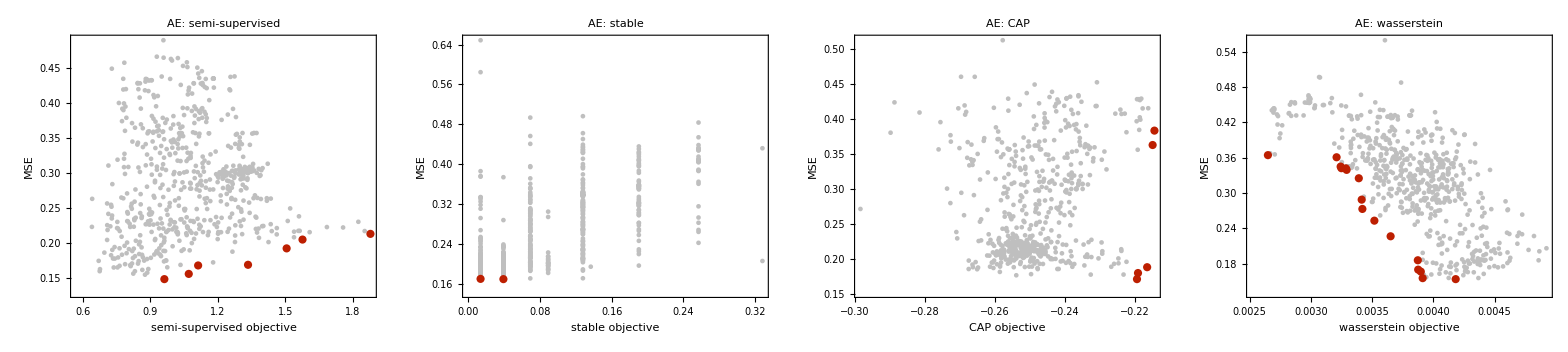

```mathematica
frontRowAE = modelFrontRow[rebuttalFrontsDir, "ae", "AE"]
Export[rebuttalOutDir <> "fronts_ae" <> rebuttalTierSuffix <> ".svg", frontRowAE, "SVG"];
Export[rebuttalOutDir <> "fronts_ae" <> rebuttalTierSuffix <> ".pdf", frontRowAE, "PDF"];
```

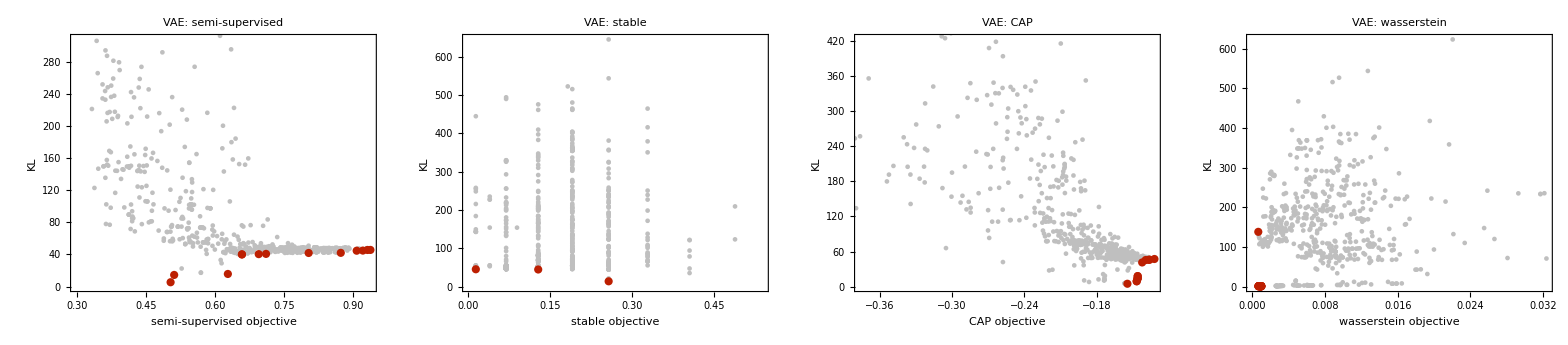

```mathematica
frontRowVAE = modelFrontRow[rebuttalFrontsDir, "vae", "VAE"]
Export[rebuttalOutDir <> "fronts_vae" <> rebuttalTierSuffix <> ".svg", frontRowVAE, "SVG"];
Export[rebuttalOutDir <> "fronts_vae" <> rebuttalTierSuffix <> ".pdf", frontRowVAE, "PDF"];
```

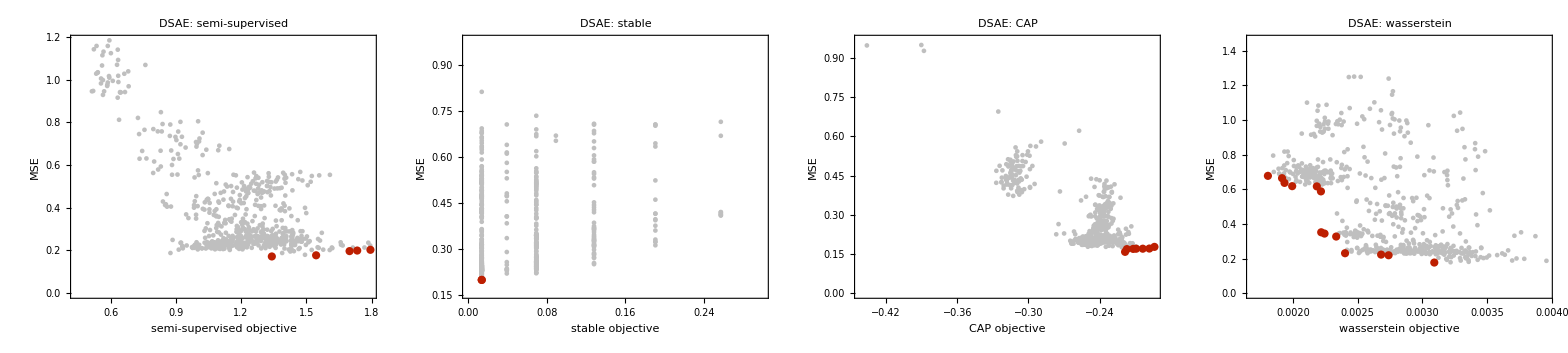

```mathematica
frontRowDSAE = modelFrontRow[rebuttalFrontsDir, "dsae", "DSAE"]
Export[rebuttalOutDir <> "fronts_dsae" <> rebuttalTierSuffix <> ".svg", frontRowDSAE, "SVG"];
Export[rebuttalOutDir <> "fronts_dsae" <> rebuttalTierSuffix <> ".pdf", frontRowDSAE, "PDF"];
```

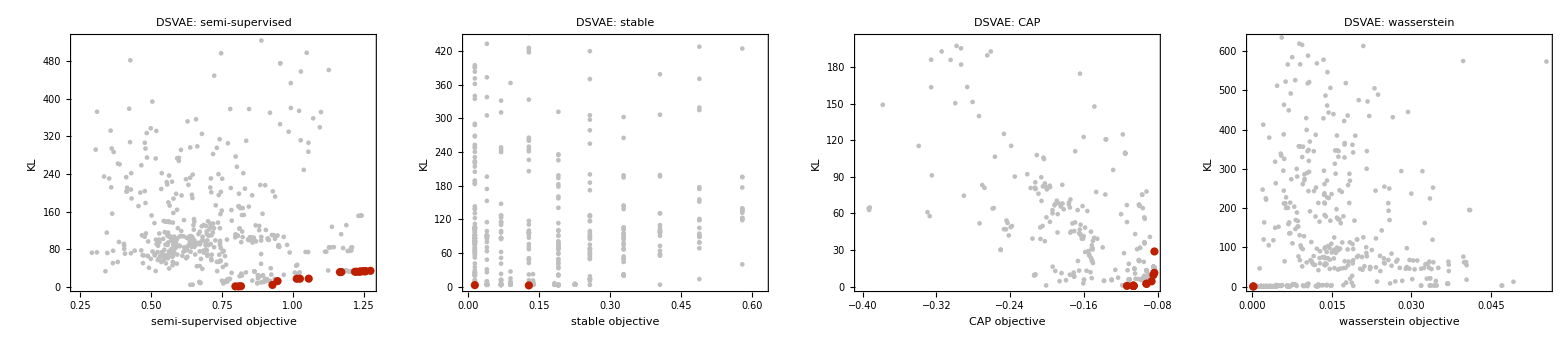

```mathematica
frontRowDSVAE = modelFrontRow[rebuttalFrontsDir, "dsvae", "DSVAE"]
Export[rebuttalOutDir <> "fronts_dsvae" <> rebuttalTierSuffix <> ".svg", frontRowDSVAE, "SVG"];
Export[rebuttalOutDir <> "fronts_dsvae" <> rebuttalTierSuffix <> ".pdf", frontRowDSVAE, "PDF"];
```

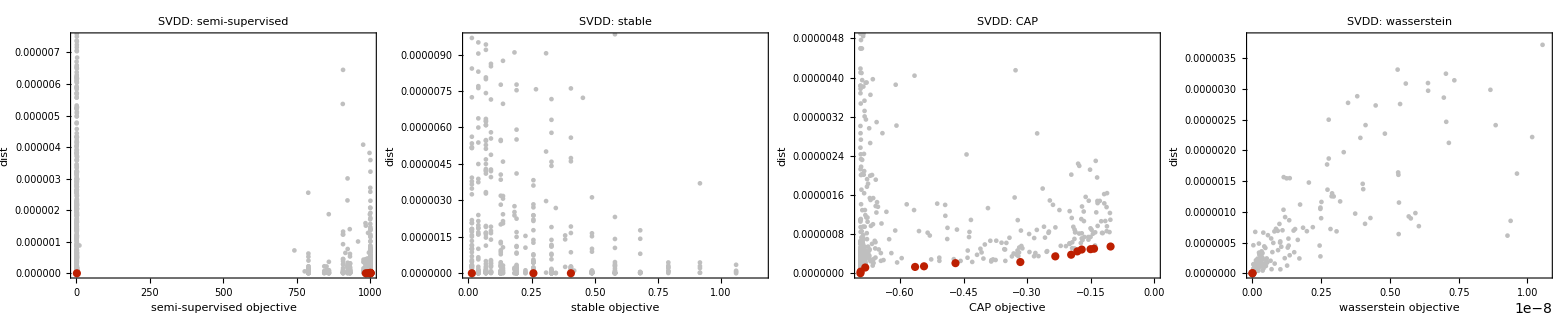

```mathematica
frontRowSVDD = modelFrontRow[rebuttalFrontsDir, "svdd", "SVDD"]
Export[rebuttalOutDir <> "fronts_svdd" <> rebuttalTierSuffix <> ".svg", frontRowSVDD, "SVG"];
Export[rebuttalOutDir <> "fronts_svdd" <> rebuttalTierSuffix <> ".pdf", frontRowSVDD, "PDF"];
```

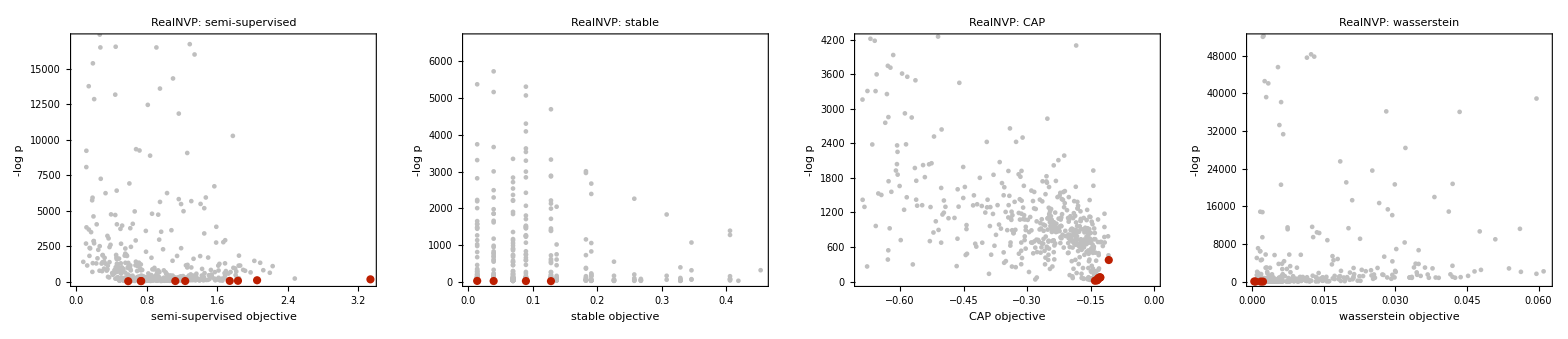

```mathematica
frontRowRealNVP = modelFrontRow[rebuttalFrontsDir, "realnvp", "RealNVP"]
Export[rebuttalOutDir <> "fronts_realnvp" <> rebuttalTierSuffix <> ".svg", frontRowRealNVP, "SVG"];
Export[rebuttalOutDir <> "fronts_realnvp" <> rebuttalTierSuffix <> ".pdf", frontRowRealNVP, "PDF"];
```

## Legacy Pareto Point Selection (by hand)

### 1. Tables

```mathematica
allArchitectures250hz=<|
"AE"-><|
"semisupervised"->{0.31,0.53,0.00,0.17,1.79,1.05,0.96,17.05,17.50,21.16,1.92,0.06,16.86,15.76,15.65,7.14,0.59,0.33,0.58,17.41},
"CAP"->{0.18,0.44,0.00,0.05,0.98,0.87,0.98,13.67,14.24,18.44,0.82,0.04,14.97,13.93,12.62,3.82,0.36,0.41,1.18,16.67},
"stable"->{2.97,0.39,0.00,0.14,0.81,0.67,0.72,9.52,9.81,14.43,0.62,0.04,12.24,9.46,8.23,2.84,0.29,0.30,0.48,11.91},
"wasserstein"->{0.16,0.22,0.00,0.03,0.77,0.57,0.66,5.38,5.42,14.82,0.51,0.02,12.21,5.47,5.32,2.45,0.20,0.18,0.33,9.64}
|>,
"VAE"-><|
"semisupervised"->{0.02,0.18,0.00,0.00,0.77,0.86,1.02,8.43,8.88,18.93,0.68,0.04,12.44,10.11,9.15,2.79,0.32,0.24,0.38,15.93},
"CAP"->{0.02,0.20,0.00,0.00,0.82,0.93,1.10,8.87,9.35,19.74,0.73,0.04,12.93,10.70,9.60,2.93,0.32,0.24,0.40,16.83},
"stable"->{0.02,0.19,0.00,0.01,0.95,1.03,1.15,6.34,6.56,21.12,0.65,0.04,15.36,8.08,7.14,2.34,0.33,0.21,0.36,15.90},
"wasserstein"->{0.02,0.21,0.00,0.01,0.91,1.07,1.17,5.77,5.92,23.70,0.78,0.04,15.10,7.62,6.77,2.76,0.32,0.12,0.18,17.37}
|>,
"DSAE"-><|
"semisupervised"->{0.47,0.59,0.00,0.10,1.22,1.04,1.16,24.23,25.34,17.00,1.16,0.05,13.27,21.69,21.13,6.43,0.40,0.60,1.00,19.04},
"CAP"->{0.39,0.61,0.00,0.10,1.23,1.08,1.20,26.20,26.86,20.58,1.12,0.05,15.23,23.61,23.15,6.91,0.43,0.68,1.12,20.36},
"stable"->{1.01,0.33,0.00,0.04,0.86,0.56,0.68,6.52,6.58,14.04,0.60,0.02,11.11,5.88,6.23,2.13,0.26,0.73,4.65,9.09},
"wasserstein"->{0.15,1.74,0.00,0.02,1.04,0.72,0.84,6.25,6.60,15.32,0.66,0.03,12.84,6.37,6.33,2.67,0.31,0.47,1.36,11.24}
|>,
"DSVAE"-><|
"semisupervised"->{0.11,0.18,0.00,0.01,1.18,0.97,1.12,12.13,12.89,17.85,0.77,0.04,14.00,13.12,11.79,3.63,0.38,0.44,0.76,16.27},
"CAP"->{0.02,0.19,0.00,0.01,1.10,1.02,1.15,9.51,10.00,19.45,0.70,0.04,15.23,11.09,9.72,3.16,0.37,0.27,0.46,16.87},
"stable"->{0.01,0.55,0.00,0.01,0.77,1.02,1.18,9.01,9.50,20.08,0.88,0.04,13.04,11.17,9.46,2.67,0.28,0.21,0.35,16.81},
"wasserstein"->{0.05,0.33,0.00,0.01,0.31,0.15,0.13,1.40,1.53,3.99,0.32,0.02,2.41,0.91,1.21,1.28,0.11,0.03,0.05,1.85}
|>,
"SVDD"-><|
"semisupervised"->{0.44,0.14,0.00,1.01,0.90,0.72,0.78,5.23,4.75,16.16,0.67,0.04,11.13,5.35,5.70,2.29,0.24,0.24,0.65,9.50},
"CAP"->{1.14,0.19,0.00,0.05,0.71,0.68,0.81,9.06,9.21,13.26,0.83,0.03,10.59,8.88,8.48,2.99,0.27,0.44,0.72,12.24},
"stable"->{0.50,0.19,0.01,0.11,1.09,0.69,0.58,8.81,8.89,8.40,1.93,0.05,8.41,7.73,7.50,6.27,0.37,0.05,0.06,9.61},
"wasserstein"->{0.71,0.09,0.00,0.03,0.55,0.46,0.58,7.57,7.98,13.30,0.38,0.02,9.92,6.44,6.05,1.91,0.20,0.09,0.14,8.63}
|>,
"RealNVP"-><|
"semisupervised"->{1.13,0.15,0.02,0.20,1.07,0.77,0.90,11.70,12.06,13.67,0.93,0.07,10.29,10.45,10.66,3.46,0.41,1.95,9.18,11.67},
"CAP"->{2.55,0.04,0.00,0.71,0.49,0.31,0.28,12.71,12.80,3.98,0.61,0.06,3.86,9.81,8.85,2.87,0.19,0.16,0.39,4.59},
"stable"->{1.47,0.04,0.00,0.17,0.34,0.36,0.37,12.19,12.77,3.79,0.54,0.04,4.60,9.92,8.83,2.26,0.14,0.15,0.23,5.09},
"wasserstein"->{0.99,0.02,0.00,0.58,0.18,0.19,0.21,6.25,6.29,1.99,0.25,0.04,2.19,5.28,4.72,1.15,0.13,0.08,0.16,2.50}
|>
|>;
compactTableTex=BuildLatexTableCompactAsymCollapse[allArchitectures250hz,10000,0.05,2];
printTable[compactTableTex];
Print[BuildMarkdownTableCompactAsymCollapse[allArchitectures250hz,10000,0.05,2]];
```

\begin{tabular}{lcccccccc}
\toprule
Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\
\midrule
AE & 6.84 & 5.73 & 4.29 & 3.22 & $1.44^{+0.95}_{-0.91}$ & 0.007 & $2.52^{+1.53}_{-1.35}$ & <0.001 \\
VAE & 4.56 & 4.79 & 4.39 & 4.49 & $0.40^{+0.57}_{-0.55}$ & 0.629 & $0.30^{+0.74}_{-0.74}$ & 0.659 \\
DSAE & 7.80 & 8.55 & 3.57 & 3.75 & $4.98^{+3.45}_{-3.09}$ & 0.014 & $4.80^{+3.28}_{-2.97}$ & 0.007 \\
DSVAE & 5.38 & 5.02 & 4.85 & 0.80 & $0.17^{+0.27}_{-0.20}$ & 0.629 & $4.21^{+2.52}_{-2.28}$ & <0.001 \\
SVDD & 3.30 & 4.03 & 3.56 & 3.25 & $0.47^{+0.70}_{-0.66}$ & 0.603 & $0.78^{+0.45}_{-0.40}$ & <0.001 \\
RealNVP & 5.04 & 3.26 & 3.17 & 1.66 & $0.10^{+0.17}_{-0.16}$ & 0.629 & $1.60^{+0.99}_{-0.84}$ & <0.001 \\
\bottomrule
\end{tabular}
% legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

| Arch. | Semi | CAP | Stable | W1 | CAP-Stable | p | CAP-W1 | p |
|---|---|---|---|---|---|---|---|---|
| AE | 6.84 | 5.73 | 4.29 | 3.22 | $1.44^{+0.94}_{-0.91}$ | 0.007 | $2.52^{+1.51}_{-1.38}$ | <0.001 |
| VAE | 4.56 | 4.79 | 4.39 | 4.49 | $0.40^{+0.58}_{-0.56}$ | 0.629 | $0.30^{+0.75}_{-0.74}$ | 0.659 |
| DSAE | 7.80 | 8.55 | 3.57 | 3.75 | $4.98^{+3.43}_{-3.16}$ | 0.014 | $4.80^{+3.43}_{-2.98}$ | 0.007 |
| DSVAE | 5.38 | 5.02 | 4.85 | 0.80 | $0.17^{+0.27}_{-0.20}$ | 0.629 | $4.21^{+2.55}_{-2.25}$ | <0.001 |
| SVDD | 3.30 | 4.03 | 3.56 | 3.25 | $0.47^{+0.70}_{-0.66}$ | 0.603 | $0.78^{+0.46}_{-0.39}$ | <0.001 |
| RealNVP | 5.04 | 3.26 | 3.17 | 1.66 | $0.10^{+0.17}_{-0.16}$ | 0.629 | $1.60^{+0.98}_{-0.85}$ | <0.001 |

legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

```mathematica
allArchitecturesQ99=<|
"AE"->
<|
"semisupervised"->{42.88,29.50,1.79,28.03,70.93,62.94,64.11,97.41,97.81,89.64,81.17,16.64,72.94,95.56,96.39,87.72,38.59,74.33,85.60,99.20},
"CAP"->{39.15,17.96,2.45,24.93,63.18,60.75,62.76,97.66,97.99,89.29,80.69,15.57,72.04,96.50,96.50,86.07,31.32,69.21,81.74,99.22},
"stable"->{42.02,25.64,1.86,25.51,72.09,67.16,69.69,97.68,98.08,91.25,85.01,17.41,75.34,96.32,96.52,87.75,38.47,75.25,86.08,99.48},
"wasserstein"->{36.12,13.92,2.05,29.49,58.33,56.12,59.11,96.90,97.38,85.85,72.07,13.80,67.73,95.52,95.43,81.77,26.28,65.96,78.85,97.81}
|>,
"VAE"->
<|
"semisupervised"->{52.97,29.83,1.13,37.04,77.87,68.88,72.95,99.27,99.40,93.33,91.35,24.73,80.01,98.87,98.92,94.89,55.58,85.09,92.09,99.82},
"CAP"->{51.20,29.65,1.42,28.61,80.22,72.93,76.38,99.62,99.70,94.01,92.30,31.04,81.48,99.42,99.43,96.44,58.54,85.76,92.50,99.77},
"stable"->{28.53,12.95,0.94,4.31,66.47,58.22,62.85,96.64,96.97,91.61,88.13,18.55,76.63,96.29,97.04,90.42,42.93,79.82,88.57,99.47},
"wasserstein"->{32.07,13.91,1.10,5.54,66.34,58.47,62.83,98.64,98.81,91.65,88.16,20.70,77.14,98.23,98.31,92.34,45.69,82.22,89.71,99.45}
|>,
"DSAE"-><|
"semisupervised"->{39.85,33.24,1.66,29.69,69.31,61.43,64.87,98.20,98.52,90.27,84.07,15.58,73.85,97.01,97.35,89.51,38.35,75.79,86.89,99.59},
"CAP"->{32.00,13.64,2.12,19.83,56.61,51.48,54.60,95.83,96.38,85.91,73.04,10.89,67.00,93.80,94.04,79.84,24.74,57.40,73.84,98.15},
"stable"->{34.29,12.32,1.99,21.52,54.37,49.06,51.85,96.70,97.19,85.84,73.32,10.52,67.07,94.97,95.06,80.25,23.81,64.76,77.33,98.33},
"wasserstein"->{35.19,15.12,1.70,23.24,56.07,49.45,52.75,96.41,96.94,87.46,77.44,10.62,69.12,94.64,94.82,80.69,26.15,66.53,79.65,98.80}
|>,
"DSVAE"-><|
"semisupervised"->{54.88,30.67,1.47,43.45,79.62,73.19,77.08,99.58,99.65,94.27,92.70,30.04,81.86,99.37,99.36,96.15,58.67,85.27,92.34,99.81},
"CAP"->{55.71,30.01,1.37,38.88,80.55,73.49,77.67,99.42,99.53,94.15,92.66,27.94,81.29,99.13,99.18,95.76,59.44,87.15,93.29,99.84},
"stable"->{38.46,34.41,1.51,44.53,56.00,52.41,49.99,97.32,97.43,89.88,84.81,26.61,74.31,96.91,96.94,88.38,37.00,36.53,62.19,98.82},
"wasserstein"->{34.39,23.17,1.09,10.98,51.54,43.86,42.55,89.02,88.64,86.88,77.23,11.85,68.69,88.09,89.38,77.90,28.50,56.26,76.71,97.38}
|>,
"SVDD"-><|
"semisupervised"->{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},
"CAP"->{31.14,7.99,1.14,5.04,58.28,51.71,55.04,97.46,97.75,89.59,84.23,14.31,73.29,96.81,97.03,87.95,32.81,73.76,84.11,99.40},
"stable"->{43.72,16.03,1.99,17.61,67.25,61.34,66.32,95.99,96.42,91.01,86.48,19.04,75.83,95.29,95.21,86.91,44.13,81.72,89.96,99.44},
"wasserstein"->{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
|>,
"RealNVP"-><|
"semisupervised"->{56.09,18.69,1.70,48.78,81.25,76.74,79.52,99.64,99.69,94.13,92.36,27.38,80.96,99.37,99.32,95.63,53.18,83.01,91.76,99.81},
"CAP"->{15.69,0.93,2.95,20.13,26.50,27.59,27.41,88.25,88.59,43.85,27.29,12.19,35.05,83.07,82.14,56.58,15.34,19.89,26.28,57.32},
"stable"->{20.54,0.87,2.43,23.64,23.86,23.78,22.93,85.05,85.16,41.03,25.09,11.07,33.36,78.36,78.00,52.98,14.30,22.98,34.02,52.36},
"wasserstein"->{17.88,1.34,1.93,23.86,20.34,21.50,20.52,85.52,85.73,39.47,23.39,9.91,32.17,79.78,78.59,51.93,12.24,15.57,18.99,52.27}
|>
|>;
compactTableTex=BuildLatexTableCompactAsymCollapse[allArchitecturesQ99,10000,0.05,2];
printTable[compactTableTex];
Print[BuildMarkdownTableCompactAsymCollapse[allArchitecturesQ99,10000,0.05,2]];
```

\begin{tabular}{lcccccccc}
\toprule
Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\
\midrule
AE & 66.66 & 64.25 & 67.43 & 61.52 & $-3.18^{+1.27}_{-1.34}$ & <0.001 & $2.72^{+1.11}_{-1.18}$ & 0.002 \\
VAE & 72.70 & 73.52 & 64.87 & 66.07 & $8.65^{+3.20}_{-3.03}$ & <0.001 & $7.46^{+3.06}_{-2.99}$ & <0.001 \\
DSAE & 67.25 & 59.06 & 59.53 & 60.64 & $-0.47^{+0.91}_{-1.05}$ & 0.436 & $-1.58^{+1.03}_{-1.19}$ & 0.017 \\
DSVAE & 74.47 & 74.32 & 63.22 & 57.21 & $11.10^{+6.53}_{-5.74}$ & 0.003 & $17.12^{+4.52}_{-4.33}$ & <0.001 \\
SVDD & coll & 61.94 & 66.58 & coll & $-4.64^{+2.22}_{-2.29}$ & 0.011 & n/a & n/a \\
RealNVP & 73.95 & 37.85 & 36.59 & 34.65 & $1.26^{+1.38}_{-1.59}$ & 0.179 & $3.21^{+1.16}_{-1.27}$ & 0.002 \\
\bottomrule
\end{tabular}
% legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

| Arch. | Semi | CAP | Stable | W1 | CAP-Stable | p | CAP-W1 | p |
|---|---|---|---|---|---|---|---|---|
| AE | 66.66 | 64.25 | 67.43 | 61.52 | $-3.18^{+1.28}_{-1.32}$ | <0.001 | $2.72^{+1.10}_{-1.14}$ | 0.002 |
| VAE | 72.70 | 73.52 | 64.87 | 66.07 | $8.65^{+3.22}_{-3.07}$ | <0.001 | $7.46^{+3.15}_{-3.00}$ | <0.001 |
| DSAE | 67.25 | 59.06 | 59.53 | 60.64 | $-0.47^{+0.89}_{-1.02}$ | 0.436 | $-1.58^{+1.04}_{-1.19}$ | 0.017 |
| DSVAE | 74.47 | 74.32 | 63.22 | 57.21 | $11.10^{+6.38}_{-5.71}$ | 0.003 | $17.12^{+4.44}_{-4.27}$ | <0.001 |
| SVDD | coll | 61.94 | 66.58 | coll | $-4.64^{+2.18}_{-2.28}$ | 0.011 | n/a | n/a |
| RealNVP | 73.95 | 37.85 | 36.59 | 34.65 | $1.26^{+1.35}_{-1.60}$ | 0.179 | $3.21^{+1.14}_{-1.25}$ | 0.002 |

legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

### 2. Plots

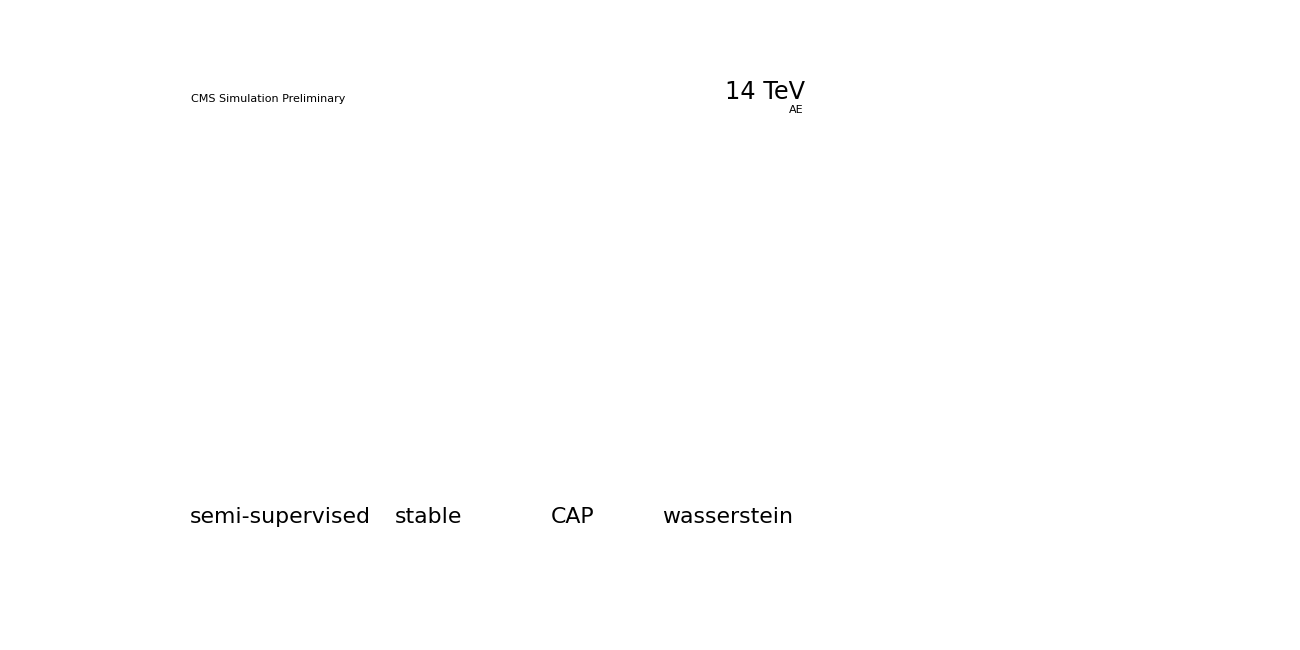
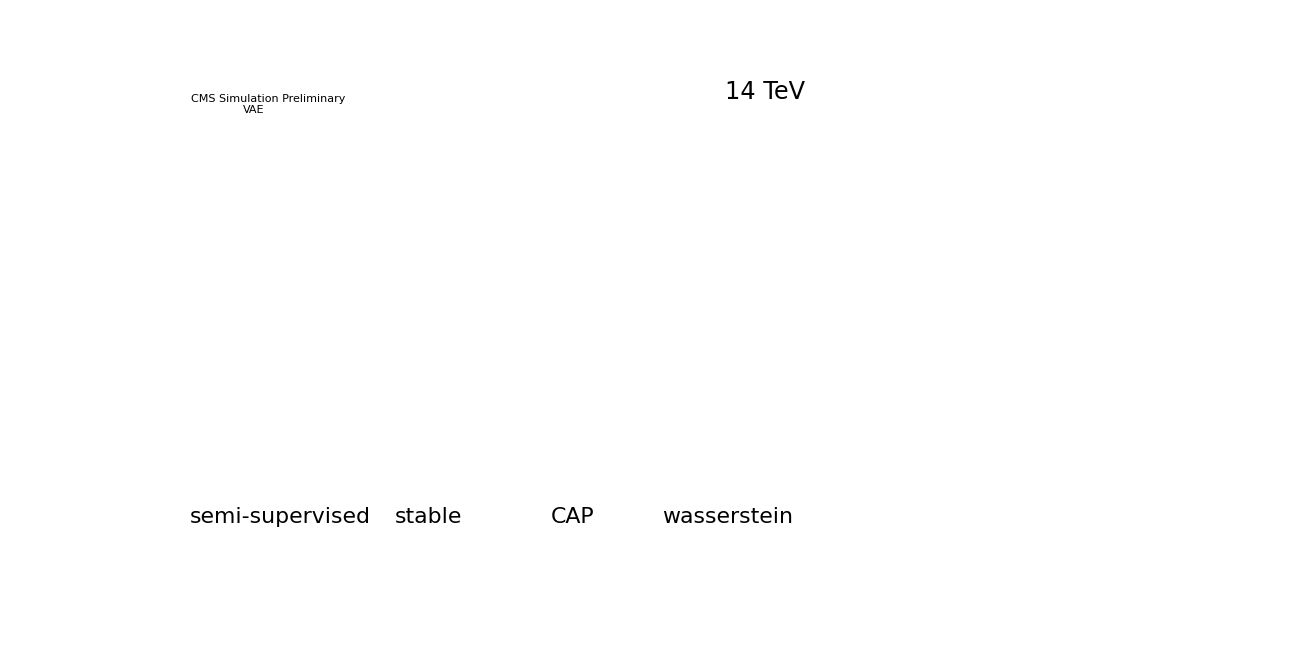
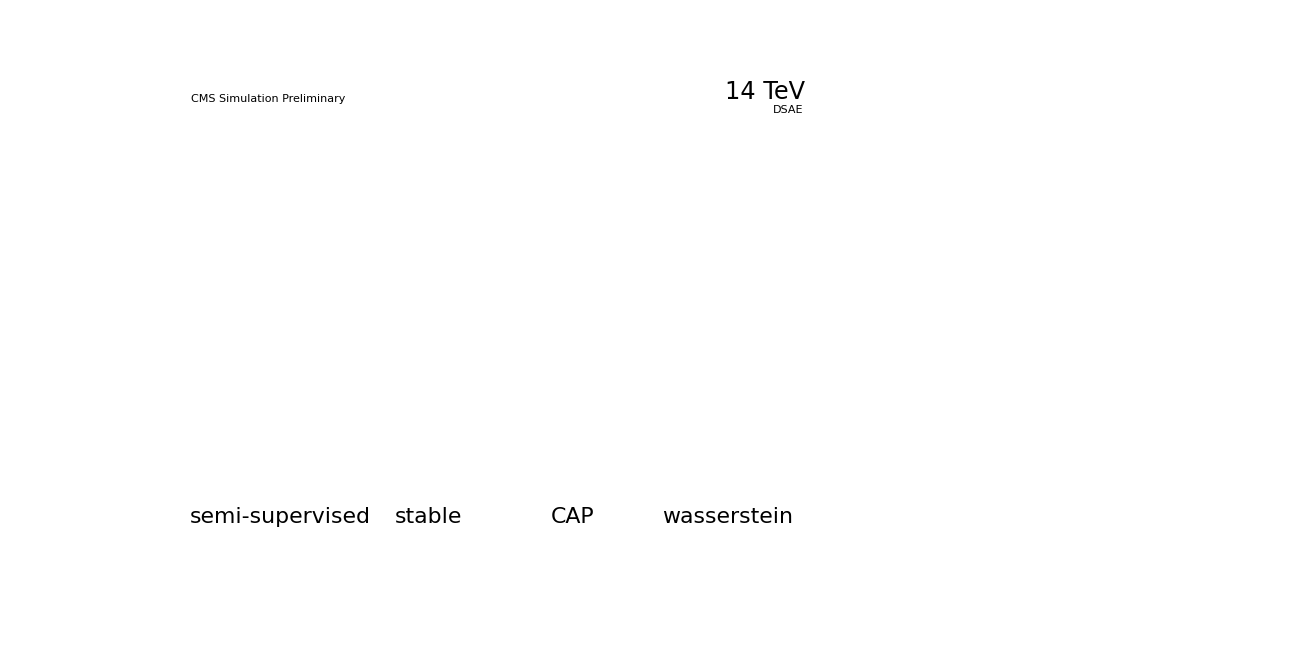
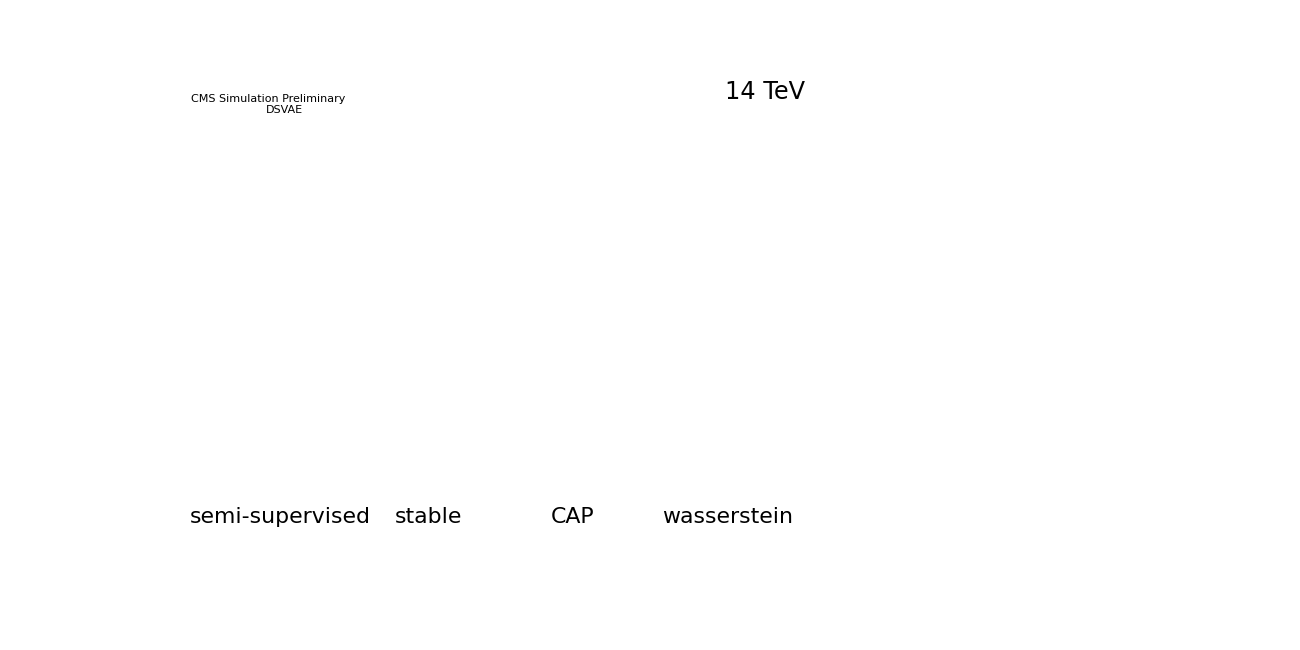
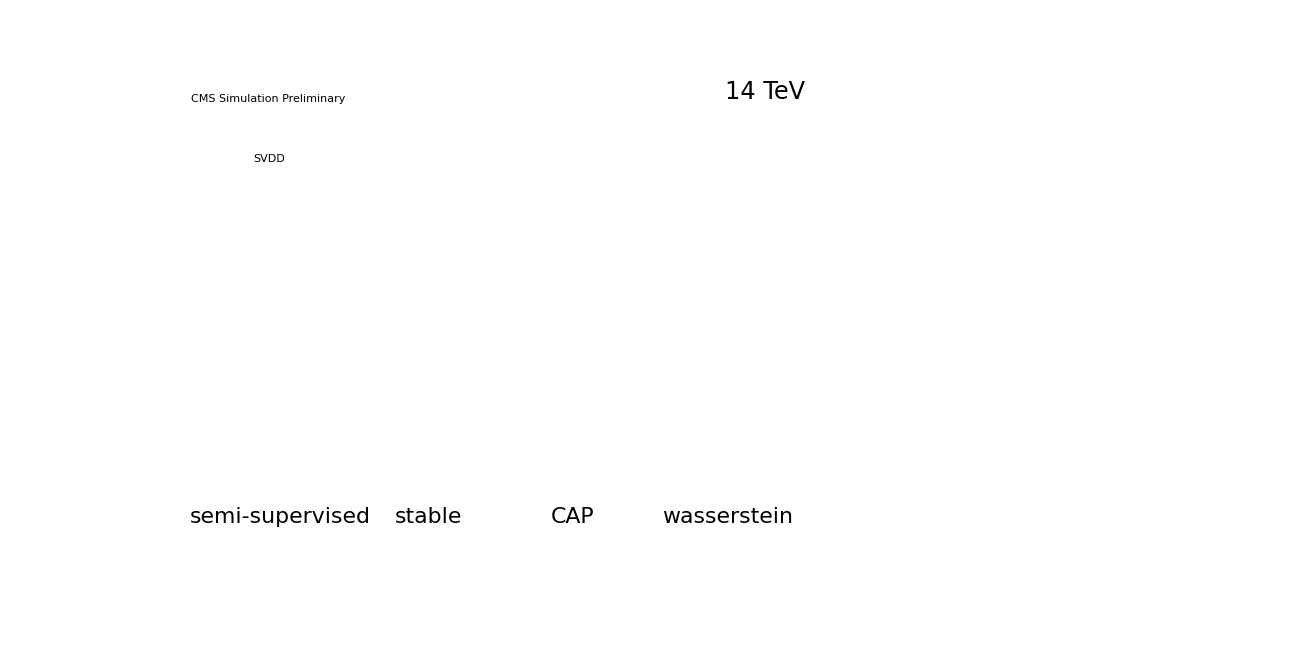
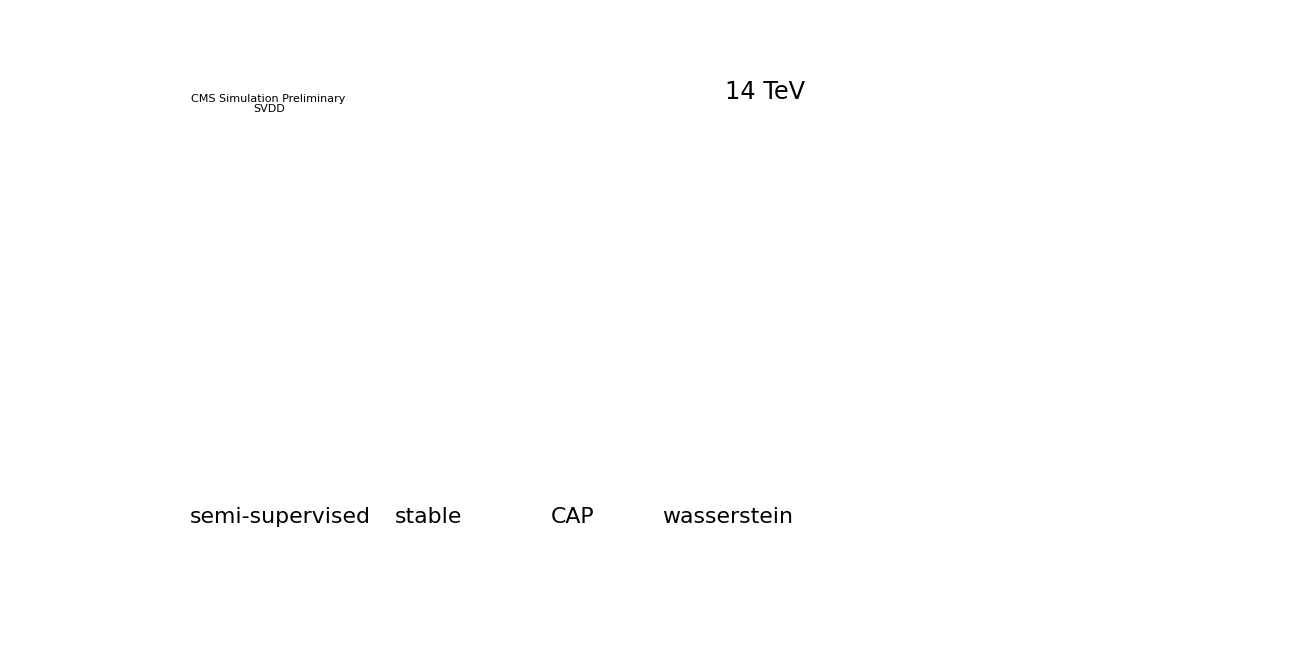
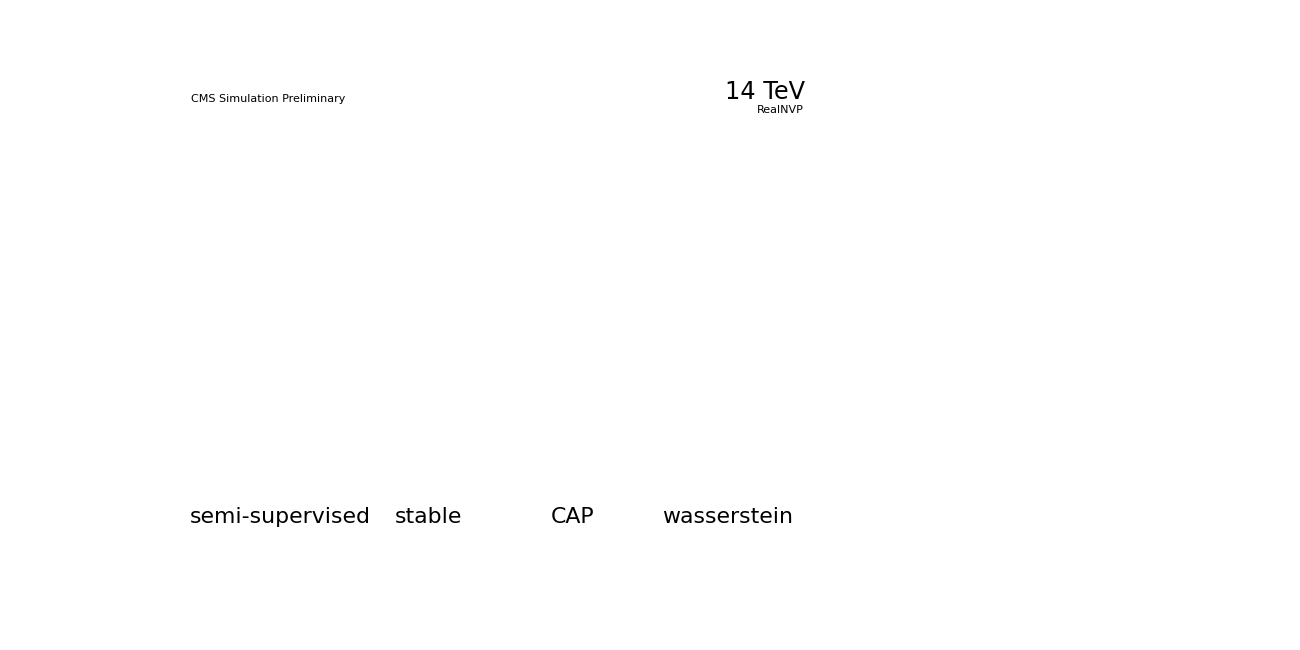
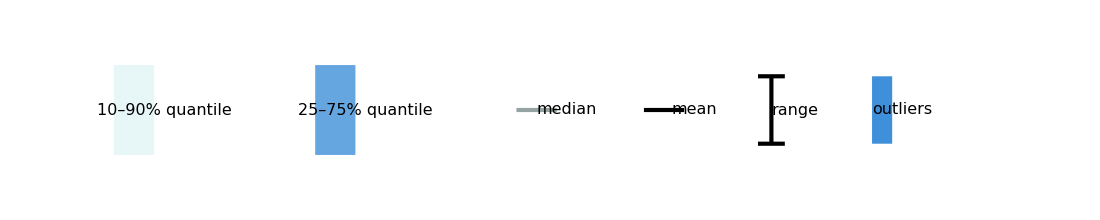
```mathematica
(*Data AE @ 250Hz*)
semisupervised={0.31,0.53,0.00,0.17,1.79,1.05,0.96,17.05,17.50,21.16,1.92,0.06,16.86,15.76,15.65,7.14,0.59,0.33,0.58,17.41};
CAP={0.18,0.44,0.00,0.05,0.98,0.87,0.98,13.67,14.24,18.44,0.82,0.04,14.97,13.93,12.62,3.82,0.36,0.41,1.18,16.67};
stable={2.97,0.39,0.00,0.14,0.81,0.67,0.72,9.52,9.81,14.43,0.62,0.04,12.24,9.46,8.23,2.84,0.29,0.30,0.48,11.91};
wasserstein={0.16,0.22,0.00,0.03,0.77,0.57,0.66,5.38,5.42,14.82,0.51,0.02,12.21,5.47,5.32,2.45,0.20,0.18,0.33,9.64};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17, "AE"]
Export["effs/" <> "ae_250Hz" <>".svg",plot,"SVG"]
Export["effs/" <> "ae_250Hz" <>".pdf",plot,"PDF"]
Export["effs/" <> "ae_250Hz" <>".jpeg",plot,"JPEG"]
-Graphics-
"effs/ae_250Hz.svg"
"effs/ae_250Hz.pdf"
"effs/ae_250Hz.jpeg"
Efficiency Plot:AE@q99
(*Physics efficiencies@q99—AE architecture*)
semisupervised={0.4288,0.2950,0.0179,0.2803,0.7093,0.6294,0.6411,0.9741,0.9781,0.8964,0.8117,0.1664,0.7294,0.9556,0.9639,0.8772,0.3859,0.7433,0.8560,0.9920}*100;
CAP={0.3915,0.1796,0.0245,0.2493,0.6318,0.6075,0.6276,0.9766,0.9799,0.8929,0.8069,0.1557,0.7204,0.9650,0.9650,0.8607,0.3132,0.6921,0.8174,0.9922}*100;
stable={0.4202,0.2564,0.0186,0.2551,0.7209,0.6716,0.6969,0.9768,0.9808,0.9125,0.8501,0.1741,0.7534,0.9632,0.9652,0.8775,0.3847,0.7525,0.8608,0.9948}*100;
wasserstein={0.3612,0.1392,0.0205,0.2949,0.5833,0.5612,0.5911,0.9690,0.9738,0.8585,0.7207,0.1380,0.6773,0.9552,0.9543,0.8177,0.2628,0.6596,0.7885,0.9781}*100;

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17, "AE"]
Export["effs/" <> "ae_q99" <>".svg",plot,"SVG"]
Export["effs/" <> "ae_q99" <>".pdf",plot,"PDF"]
Export["effs/" <> "ae_q99" <>".jpeg",plot,"JPEG"]
-Graphics-
"effs/ae_q99.svg"
"effs/ae_q99.pdf"
"effs/ae_q99.jpeg"
Efficiency Plot:VAE@250 Hz
(*Data VAE*)
semisupervised={0.02,0.18,0.00,0.00,0.77,0.86,1.02,8.43,8.88,18.93,0.68,0.04,12.44,10.11,9.15,2.79,0.32,0.24,0.38,15.93};
CAP={0.02,0.20,0.00,0.00,0.82,0.93,1.10,8.87,9.35,19.74,0.73,0.04,12.93,10.70,9.60,2.93,0.32,0.24,0.40,16.83};
stable={0.02,0.19,0.00,0.01,0.95,1.03,1.15,6.34,6.56,21.12,0.65,0.04,15.36,8.08,7.14,2.34,0.33,0.21,0.36,15.90};
wasserstein={0.02,0.21,0.00,0.01,0.91,1.07,1.17,5.77,5.92,23.70,0.78,0.04,15.10,7.62,6.77,2.76,0.32,0.12,0.18,17.37};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"VAE", {0.151, 0.899}]
Export["effs/" <> "vae_250Hz" <>".svg",plot,"SVG"]
Export["effs/" <> "vae_250Hz" <>".pdf",plot,"PDF"]
Export["effs/" <> "vae_250Hz" <>".jpeg",plot,"JPEG"]
-Graphics-
"effs/vae_250Hz.svg"
"effs/vae_250Hz.pdf"
"effs/vae_250Hz.jpeg"
Export["effs/" <> "vae_250Hz" <>".pdf",plot,"PDF"]
Efficiency Plot:VAE@q99

(*Physics efficiencies@q99—VAE architecture*)
semisupervised={0.5297,0.2983,0.0113,0.3704,0.7787,0.6888,0.7295,0.9927,0.9940,0.9333,0.9135,0.2473,0.8001,0.9887,0.9892,0.9489,0.5558,0.8509,0.9209,0.9982}*100;
CAP={0.5120,0.2965,0.0142,0.2861,0.8022,0.7293,0.7638,0.9962,0.9970,0.9401,0.9230,0.3104,0.8148,0.9942,0.9943,0.9644,0.5854,0.8576,0.9250,0.9977}*100;
stable={0.2853,0.1295,0.0094,0.0431,0.6647,0.5822,0.6285,0.9664,0.9697,0.9161,0.8813,0.1855,0.7663,0.9629,0.9704,0.9042,0.4293,0.7982,0.8857,0.9947}*100;
wasserstein={0.3207,0.1391,0.0110,0.0554,0.6634,0.5847,0.6283,0.9864,0.9881,0.9165,0.8816,0.2070,0.7714,0.9823,0.9831,0.9234,0.4569,0.8222,0.8971,0.9945}*100;

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17, "VAE",{0.151, 0.899}]
Export["effs/" <> "vae_q99" <>".svg",plot,"SVG"]
Export["effs/" <> "vae_q99" <>".pdf",plot,"PDF"]
Export["effs/" <> "vae_q99" <>".jpeg",plot,"JPEG"]
-Graphics-
"effs/vae_q99.svg"
"effs/vae_q99.pdf"
"effs/vae_q99.jpeg"
Efficiency Plot:DS AE@250 Hz
(*Data DS AE*)
semisupervised={0.47,0.59,0.00,0.10,1.22,1.04,1.16,24.23,25.34,17.00,1.16,0.05,13.27,21.69,21.13,6.43,0.40,0.60,1.00,19.04};
CAP={0.39,0.61,0.00,0.10,1.23,1.08,1.20,26.20,26.86,20.58,1.12,0.05,15.23,23.61,23.15,6.91,0.43,0.68,1.12,20.36};
stable={1.01,0.33,0.00,0.04,0.86,0.56,0.68,6.52,6.58,14.04,0.60,0.02,11.11,5.88,6.23,2.13,0.26,0.73,4.65,9.09};
wasserstein={0.15,1.74,0.00,0.02,1.04,0.72,0.84,6.25,6.60,15.32,0.66,0.03,12.84,6.37,6.33,2.67,0.31,0.47,1.36,11.24};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"DSAE", {0.639, 0.899}]
Export["effs/" <> "dsae_250Hz" <>".svg",plot,"SVG"]
Export["effs/" <> "dsae_250Hz" <>".pdf",plot,"PDF"]
Export["effs/" <> "dsae_250Hz" <>".jpeg",plot,"JPEG"]
-Graphics-
"effs/dsae_250Hz.svg"
"effs/dsae_250Hz.pdf"
"effs/dsae_250Hz.jpeg"
Efficiency Plot:DS AE@q99
(*Data DS AE*)
semisupervised={39.85,33.24,1.66,29.69,69.31,61.43,64.87,98.20,98.52,90.27,84.07,15.58,73.85,97.01,97.35,89.51,38.35,75.79,86.89,99.59};
CAP={32.00,13.64,2.12,19.83,56.61,51.48,54.60,95.83,96.38,85.91,73.04,10.89,67.00,93.80,94.04,79.84,24.74,57.40,73.84,98.15};
stable={34.29,12.32,1.99,21.52,54.37,49.06,51.85,96.70,97.19,85.84,73.32,10.52,67.07,94.97,95.06,80.25,23.81,64.76,77.33,98.33};
wasserstein={35.19,15.12,1.70,23.24,56.07,49.45,52.75,96.41,96.94,87.46,77.44,10.62,69.12,94.64,94.82,80.69,26.15,66.53,79.65,98.80};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"DSAE", {0.639, 0.899}]
Export["effs/" <> "dsae_q99" <>".svg",plot,"SVG"]
Export["effs/" <> "dsae_q99" <>".pdf",plot,"PDF"]
Export["effs/" <> "dsae_q99" <>".jpeg",plot,"JPEG"]

-Graphics-
"effs/dsae_q99.svg"
"effs/dsae_q99.pdf"
"effs/dsae_q99.jpeg"
Efficiency plot:DS VAE@250 Hz

(*Data DS VAE*)
semisupervised={0.11,0.18,0.00,0.01,1.18,0.97,1.12,12.13,12.89,17.85,0.77,0.04,14.00,13.12,11.79,3.63,0.38,0.44,0.76,16.27};
CAP={0.02,0.19,0.00,0.01,1.10,1.02,1.15,9.51,10.00,19.45,0.70,0.04,15.23,11.09,9.72,3.16,0.37,0.27,0.46,16.87};
stable={0.01,0.55,0.00,0.01,0.77,1.02,1.18,9.01,9.50,20.08,0.88,0.04,13.04,11.17,9.46,2.67,0.28,0.21,0.35,16.81};
wasserstein={0.05,0.33,0.00,0.01,0.31,0.15,0.13,1.40,1.53,3.99,0.32,0.02,2.41,0.91,1.21,1.28,0.11,0.03,0.05,1.85};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"DSVAE", {0.186, 0.899}]
Export["effs/" <> "dsvae_250Hz" <>".svg",plot,"SVG"]
Export["effs/" <> "dsvae_250Hz" <>".pdf",plot,"PDF"]
Export["effs/" <> "dsvae_250Hz" <>".jpeg",plot,"JPEG"]
-Graphics-
"effs/dsvae_250Hz.svg"
"effs/dsvae_250Hz.pdf"
"effs/dsvae_250Hz.jpeg"
Efficiency Plot:DSVAE@q99
(*Data DS VAE*)
semisupervised={54.88,30.67,1.47,43.45,79.62,73.19,77.08,99.58,99.65,94.27,92.70,30.04,81.86,99.37,99.36,96.15,58.67,85.27,92.34,99.81};
CAP={55.71,30.01,1.37,38.88,80.55,73.49,77.67,99.42,99.53,94.15,92.66,27.94,81.29,99.13,99.18,95.76,59.44,87.15,93.29,99.84};
stable={38.46,34.41,1.51,44.53,56.00,52.41,49.99,97.32,97.43,89.88,84.81,26.61,74.31,96.91,96.94,88.38,37.00,36.53,62.19,98.82};
wasserstein={34.39,23.17,1.09,10.98,51.54,43.86,42.55,89.02,88.64,86.88,77.23,11.85,68.69,88.09,89.38,77.90,28.50,56.26,76.71,97.38};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"DSVAE", {0.186, 0.899}]
Export["effs/" <> "dsvae_q99" <>".svg",plot,"SVG"]
Export["effs/" <> "dsvae_q99" <>".pdf",plot,"PDF"]
Export["effs/" <> "dsvae_q99" <>".jpeg",plot,"JPEG"]
-Graphics-
"effs/dsvae_q99.svg"
"effs/dsvae_q99.pdf"
"effs/dsvae_q99.jpeg"
Efficiency Plot:SVDD@250 Hz
(*Data SVDD*)
semisupervised={0.44,0.14,0.00,1.01,0.90,0.72,0.78,5.23,4.75,16.16,0.67,0.04,11.13,5.35,5.70,2.29,0.24,0.24,0.65,9.50};
CAP={1.14,0.19,0.00,0.05,0.71,0.68,0.81,9.06,9.21,13.26,0.83,0.03,10.59,8.88,8.48,2.99,0.27,0.44,0.72,12.24};
stable={0.50,0.19,0.01,0.11,1.09,0.69,0.58,8.81,8.89,8.40,1.93,0.05,8.41,7.73,7.50,6.27,0.37,0.05,0.06,9.61};
wasserstein={0.71,0.09,0.00,0.03,0.55,0.46,0.58,7.57,7.98,13.30,0.38,0.02,9.92,6.44,6.05,1.91,0.20,0.09,0.14,8.63};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"SVDD", {0.170, 0.81}]
Export["effs/" <> "svdd_250Hz" <>".svg",plot,"SVG"]
Export["effs/" <> "svdd_250Hz" <>".pdf",plot,"PDF"]
Export["effs/" <> "svdd_250Hz" <>".jpeg",plot,"JPEG"]

-Graphics-
"effs/svdd_250Hz.svg"
"effs/svdd_250Hz.pdf"
"effs/svdd_250Hz.jpeg"
Efficiency Plot:SVDD@q99
(*Data SVDD*)
semisupervised={0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.};
CAP={0.3114,0.0799,0.0114,0.0504,0.5828,0.5171,0.5504,0.9746,0.9775,0.8959,0.8423,0.1431,0.7329,0.9681,0.9703,0.8795,0.3281,0.7376,0.8411,0.9940}*100;
stable={0.4372,0.1603,0.0199,0.1761,0.6725,0.6134,0.6632,0.9599,0.9642,0.9101,0.8648,0.1904,0.7583,0.9529,0.9521,0.8691,0.4413,0.8172,0.8996,0.9944}*100;
wasserstein={0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"SVDD", {0.170, 0.90}]
Export["effs/" <> "svdd_q99" <>".svg",plot,"SVG"]
Export["effs/" <> "svdd_q99" <>".pdf",plot,"PDF"]
Export["effs/" <> "svdd_q99" <>".jpeg",plot,"JPEG"]

-Graphics-
"effs/svdd_q99.svg"
"effs/svdd_q99.pdf"
"effs/svdd_q99.jpeg"
Efficiency Plot:RealNVP@250 Hz
(*Data RealNVP*)
semisupervised={1.13,0.15,0.02,0.20,1.07,0.77,0.90,11.70,12.06,13.67,0.93,0.07,10.29,10.45,10.66,3.46,0.41,1.95,9.18,11.67};
CAP={2.55,0.04,0.00,0.71,0.49,0.31,0.28,12.71,12.80,3.98,0.61,0.06,3.86,9.81,8.85,2.87,0.19,0.16,0.39,4.59};
stable={1.47,0.04,0.00,0.17,0.34,0.36,0.37,12.19,12.77,3.79,0.54,0.04,4.60,9.92,8.83,2.26,0.14,0.15,0.23,5.09};
wasserstein={0.99,0.02,0.00,0.58,0.18,0.19,0.21,6.25,6.29,1.99,0.25,0.04,2.19,5.28,4.72,1.15,0.13,0.08,0.16,2.50};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"RealNVP", {0.639, 0.899}]
Export["effs/" <> "realnvp_250Hz" <>".svg",plot,"SVG"]
Export["effs/" <> "realnvp_250Hz" <>".pdf",plot,"PDF"]
Export["effs/" <> "realnvp_250Hz" <>".jpeg",plot,"JPEG"]
-Graphics-
"effs/realnvp_250Hz.svg"
"effs/realnvp_250Hz.pdf"
"effs/realnvp_250Hz.jpeg"
Efficiency Plot:RealNVP@q99
(*Physics efficiencies@q99—RealNVP architecture*)
semisupervised={0.5609,0.1869,0.0170,0.4878,0.8125,0.7674,0.7952,0.9964,0.9969,0.9413,0.9236,0.2738,0.8096,0.9937,0.9932,0.9563,0.5318,0.8301,0.9176,0.9981}*100;
CAP={0.1569,0.0093,0.0295,0.2013,0.2650,0.2759,0.2741,0.8825,0.8859,0.4385,0.2729,0.1219,0.3505,0.8307,0.8214,0.5658,0.1534,0.1989,0.2628,0.5732}*100;
stable={0.2054,0.0087,0.0243,0.2364,0.2386,0.2378,0.2293,0.8505,0.8516,0.4103,0.2509,0.1107,0.3336,0.7836,0.7800,0.5298,0.1430,0.2298,0.3402,0.5236}*100;
wasserstein={0.1788,0.0134,0.0193,0.2386,0.2034,0.2150,0.2052,0.8552,0.8573,0.3947,0.2339,0.0991,0.3217,0.7978,0.7859,0.5193,0.1224,0.1557,0.1899,0.5227}*100;

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"RealNVP", {0.639, 0.899}]
Export["effs/" <> "realnvp_q99" <>".svg",plot,"SVG"]
Export["effs/" <> "realnvp_q99" <>".pdf",plot,"PDF"]
Export["effs/" <> "realnvp_q99" <>".jpeg",plot,"JPEG"]

-Graphics-
"effs/realnvp_q99.svg"
"effs/realnvp_q99.pdf"
"effs/realnvp_q99.jpeg"
legendOnly=Graphics[{{EdgeForm[None],FaceForm[Directive[RGBColor["#92dadd"],Opacity[0.22]]],Rectangle[{0,0},{0.6,0.4}]},Text[Style["10–90% quantile",FontFamily->"TeX Gyre Heros",16],{0.75,0.2},{-1,0}],{EdgeForm[None],FaceForm[Directive[RGBColor["#3f90da"],Opacity[0.8]]],Rectangle[{3.0,0},{3.6,0.4}]},Text[Style["25–75% quantile",FontFamily->"TeX Gyre Heros",16],{3.75,0.2},{-1,0}],{Directive[RGBColor["#94a4a2"],AbsoluteThickness[3]],Line[{{6.0,0.2},{6.6,0.2}}]},Text[Style["median",FontFamily->"TeX Gyre Heros",16],{6.75,0.2},{-1,0}],{Directive[Black,AbsoluteThickness[3]],Line[{{7.9,0.2},{8.5,0.2}}]},Text[Style["mean",FontFamily->"TeX Gyre Heros",16],{8.65,0.2},{-1,0}],{Directive[Black,AbsoluteThickness[3]],Line[{{9.8,0.05},{9.8,0.35}}],Line[{{9.6,0.05},{10.0,0.05}}],Line[{{9.6,0.35},{10.0,0.35}}]},Text[Style["range",FontFamily->"TeX Gyre Heros",16],{10.15,0.2},{-1,0}],{RGBColor["#3f90da"],Rectangle[{11.3,0.05},{11.6,0.35}]},Text[Style["outliers",FontFamily->"TeX Gyre Heros",16],{11.75,0.2},{-1,0}]},PlotRange->{{-0.2,13.2},{-0.2,0.6}},ImageSize->1100,Background->White]

Export["effs/" <> "legend" <>".pdf",legendOnly,"PDF"]
-Graphics-
"effs/legend.pdf"
```

-Graphics-

effs/ae_250Hz.svg

effs/ae_250Hz.pdf

effs/ae_250Hz.jpeg

-Graphics-

effs/ae_250Hz.svg

effs/ae_250Hz.pdf

effs/ae_250Hz.jpeg

Efficiency (Plot:AE[q99])

-Graphics-

effs/ae_q99.svg

effs/ae_q99.pdf

effs/ae_q99.jpeg

-Graphics-

effs/ae_q99.svg

effs/ae_q99.pdf

effs/ae_q99.jpeg

Efficiency (Plot:Hz VAE[250])

-Graphics-

effs/vae_250Hz.svg

effs/vae_250Hz.pdf

effs/vae_250Hz.jpeg

-Graphics-

effs/vae_250Hz.svg

effs/vae_250Hz.pdf

effs/vae_250Hz.jpeg

effs/vae_250Hz.pdf

Efficiency (Plot:VAE[q99])

-Graphics-

effs/vae_q99.svg

effs/vae_q99.pdf

effs/vae_q99.jpeg

-Graphics-

effs/vae_q99.svg

effs/vae_q99.pdf

effs/vae_q99.jpeg

Efficiency (Plot:DS Hz AE[250])

-Graphics-

effs/dsae_250Hz.svg

effs/dsae_250Hz.pdf

effs/dsae_250Hz.jpeg

-Graphics-

effs/dsae_250Hz.svg

effs/dsae_250Hz.pdf

effs/dsae_250Hz.jpeg

Efficiency (Plot:DS AE[q99])

-Graphics-

effs/dsae_q99.svg

effs/dsae_q99.pdf

effs/dsae_q99.jpeg

-Graphics-

effs/dsae_q99.svg

effs/dsae_q99.pdf

effs/dsae_q99.jpeg

Efficiency (plot:DS Hz VAE[250])

-Graphics-

effs/dsvae_250Hz.svg

effs/dsvae_250Hz.pdf

effs/dsvae_250Hz.jpeg

-Graphics-

effs/dsvae_250Hz.svg

effs/dsvae_250Hz.pdf

effs/dsvae_250Hz.jpeg

Efficiency (Plot:DSVAE[q99])

-Graphics-

effs/dsvae_q99.svg

effs/dsvae_q99.pdf

effs/dsvae_q99.jpeg

-Graphics-

effs/dsvae_q99.svg

effs/dsvae_q99.pdf

effs/dsvae_q99.jpeg

Efficiency (Plot:Hz SVDD[250])

-Graphics-

effs/svdd_250Hz.svg

effs/svdd_250Hz.pdf

effs/svdd_250Hz.jpeg

-Graphics-

effs/svdd_250Hz.svg

effs/svdd_250Hz.pdf

effs/svdd_250Hz.jpeg

Efficiency (Plot:SVDD[q99])

-Graphics-

effs/svdd_q99.svg

effs/svdd_q99.pdf

effs/svdd_q99.jpeg

-Graphics-

effs/svdd_q99.svg

effs/svdd_q99.pdf

effs/svdd_q99.jpeg

Efficiency (Plot:Hz RealNVP[250])

-Graphics-

effs/realnvp_250Hz.svg

effs/realnvp_250Hz.pdf

effs/realnvp_250Hz.jpeg

-Graphics-

effs/realnvp_250Hz.svg

effs/realnvp_250Hz.pdf

effs/realnvp_250Hz.jpeg

Efficiency (Plot:RealNVP[q99])

-Graphics-

effs/realnvp_q99.svg

effs/realnvp_q99.pdf

effs/realnvp_q99.jpeg

-Graphics-

effs/realnvp_q99.svg

effs/realnvp_q99.pdf

effs/realnvp_q99.jpeg

-Graphics-

effs/legend.pdf

-Graphics-

effs/legend.pdf

### 3. Quantile Comparison

```mathematica
(* Axis 1: both operating points side by side; Holm family per
   operating point. *)
printTable[QuantileAxisLatex[allArchitectures250hz, allArchitecturesQ99]];
printTable[QuantileAxisMarkdown[allArchitectures250hz, allArchitecturesQ99]];
```

\begin{tabular}{lcccccccc}
\toprule
 & \multicolumn{4}{c}{$q \approx 0.999991$ (250\,Hz)} & \multicolumn{4}{c}{$q = 0.99$} \\
Arch. & $\Delta_{\mathrm{C-S}}$ & $p$ & $\Delta_{\mathrm{C-W}}$ & $p$ & $\Delta_{\mathrm{C-S}}$ & $p$ & $\Delta_{\mathrm{C-W}}$ & $p$ \\
\midrule
AE & 1.44 & 0.007$^{*}$ & 2.52 & <0.001$^{*}$ & -3.18 & <0.001$^{*}$ & 2.72 & 0.002$^{*}$ \\
VAE & 0.40 & 0.629 & 0.30 & 0.659 & 8.65 & <0.001$^{*}$ & 7.46 & <0.001$^{*}$ \\
DSAE & 4.98 & 0.014$^{*}$ & 4.80 & 0.007$^{*}$ & -0.47 & 0.436 & -1.58 & 0.017$^{*}$ \\
DSVAE & 0.17 & 0.629 & 4.21 & <0.001$^{*}$ & 11.10 & 0.003$^{*}$ & 17.12 & <0.001$^{*}$ \\
SVDD & 0.47 & 0.603 & 0.78 & <0.001$^{*}$ & -4.64 & 0.011$^{*}$ & n/a & n/a \\
RealNVP & 0.10 & 0.629 & 1.60 & <0.001$^{*}$ & 1.26 & 0.179 & 3.21 & 0.002$^{*}$ \\
\bottomrule
\end{tabular}

| Arch. | d(C-S) tail | p | d(C-W) tail | p | d(C-S) q99 | p | d(C-W) q99 | p |
|---|---|---|---|---|---|---|---|---|
| AE | 1.44 | 0.007* | 2.52 | <0.001* | -3.18 | <0.001* | 2.72 | 0.002* |
| VAE | 0.40 | 0.629 | 0.30 | 0.659 | 8.65 | <0.001* | 7.46 | <0.001* |
| DSAE | 4.98 | 0.014* | 4.80 | 0.007* | -0.47 | 0.436 | -1.58 | 0.017* |
| DSVAE | 0.17 | 0.629 | 4.21 | <0.001* | 11.10 | 0.003* | 17.12 | <0.001* |
| SVDD | 0.47 | 0.603 | 0.78 | <0.001* | -4.64 | 0.011* | n/a | n/a |
| RealNVP | 0.10 | 0.629 | 1.60 | <0.001* | 1.26 | 0.179 | 3.21 | 0.002* |

## Best Q’

```mathematica
bestqGroups = rulePickArrays[rebuttalModelExps, bestQPick];
bestqTabRows = HolmAdjustRows[BuildArchitectureRowsCompactCollapse[toLegacyGroups[bestqGroups], 10000, 0.05]];
printTable[LatexTableFromRows[bestqTabRows, 2]];
printTable[MarkdownTableFromRows[bestqTabRows, 2]];
```

note: no harvest CSV for physics_dte_pareto -- omitting this model.

\begin{tabular}{lcccccccc}
\toprule
Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\
\midrule
AE & 6.58 & 5.87 & 3.43 & 2.89 & $2.44^{+1.38}_{-1.27}$ & 0.002 & $2.98^{+1.62}_{-1.52}$ & <0.001 \\
VAE & 4.94 & 4.73 & 3.77 & 4.72 & $0.96^{+0.73}_{-0.67}$ & 0.050 & $0.01^{+0.17}_{-0.14}$ & 1.000 \\
DSAE & 7.96 & 7.67 & 4.65 & 3.85 & $3.02^{+1.87}_{-1.69}$ & 0.002 & $3.82^{+3.03}_{-2.61}$ & 0.062 \\
DSVAE & 3.74 & 3.29 & 0.01 & 0.93 & $3.28^{+2.12}_{-1.86}$ & <0.001 & $2.36^{+1.92}_{-1.69}$ & 0.062 \\
SVDD & coll & 4.37 & 3.56 & 10.07 & $0.82^{+0.97}_{-0.85}$ & 0.359 & $-5.70^{+3.00}_{-3.30}$ & <0.001 \\
RealNVP & 5.10 & 2.25 & 2.24 & 1.95 & $0.01^{+0.62}_{-0.63}$ & 1.000 & $0.31^{+0.94}_{-0.85}$ & 1.000 \\
\bottomrule
\end{tabular}
% legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

| Arch. | Semi | CAP | Stable | W1 | CAP-Stable | p | CAP-W1 | p |
|---|---|---|---|---|---|---|---|---|
| AE | 6.58 | 5.87 | 3.43 | 2.89 | $2.44^{+1.38}_{-1.27}$ | 0.002 | $2.98^{+1.62}_{-1.52}$ | <0.001 |
| VAE | 4.94 | 4.73 | 3.77 | 4.72 | $0.96^{+0.73}_{-0.67}$ | 0.050 | $0.01^{+0.17}_{-0.14}$ | 1.000 |
| DSAE | 7.96 | 7.67 | 4.65 | 3.85 | $3.02^{+1.87}_{-1.69}$ | 0.002 | $3.82^{+3.03}_{-2.61}$ | 0.062 |
| DSVAE | 3.74 | 3.29 | 0.01 | 0.93 | $3.28^{+2.12}_{-1.86}$ | <0.001 | $2.36^{+1.92}_{-1.69}$ | 0.062 |
| SVDD | coll | 4.37 | 3.56 | 10.07 | $0.82^{+0.97}_{-0.85}$ | 0.359 | $-5.70^{+3.00}_{-3.30}$ | <0.001 |
| RealNVP | 5.10 | 2.25 | 2.24 | 1.95 | $0.01^{+0.62}_{-0.63}$ | 1.000 | $0.31^{+0.94}_{-0.85}$ | 1.000 |

legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

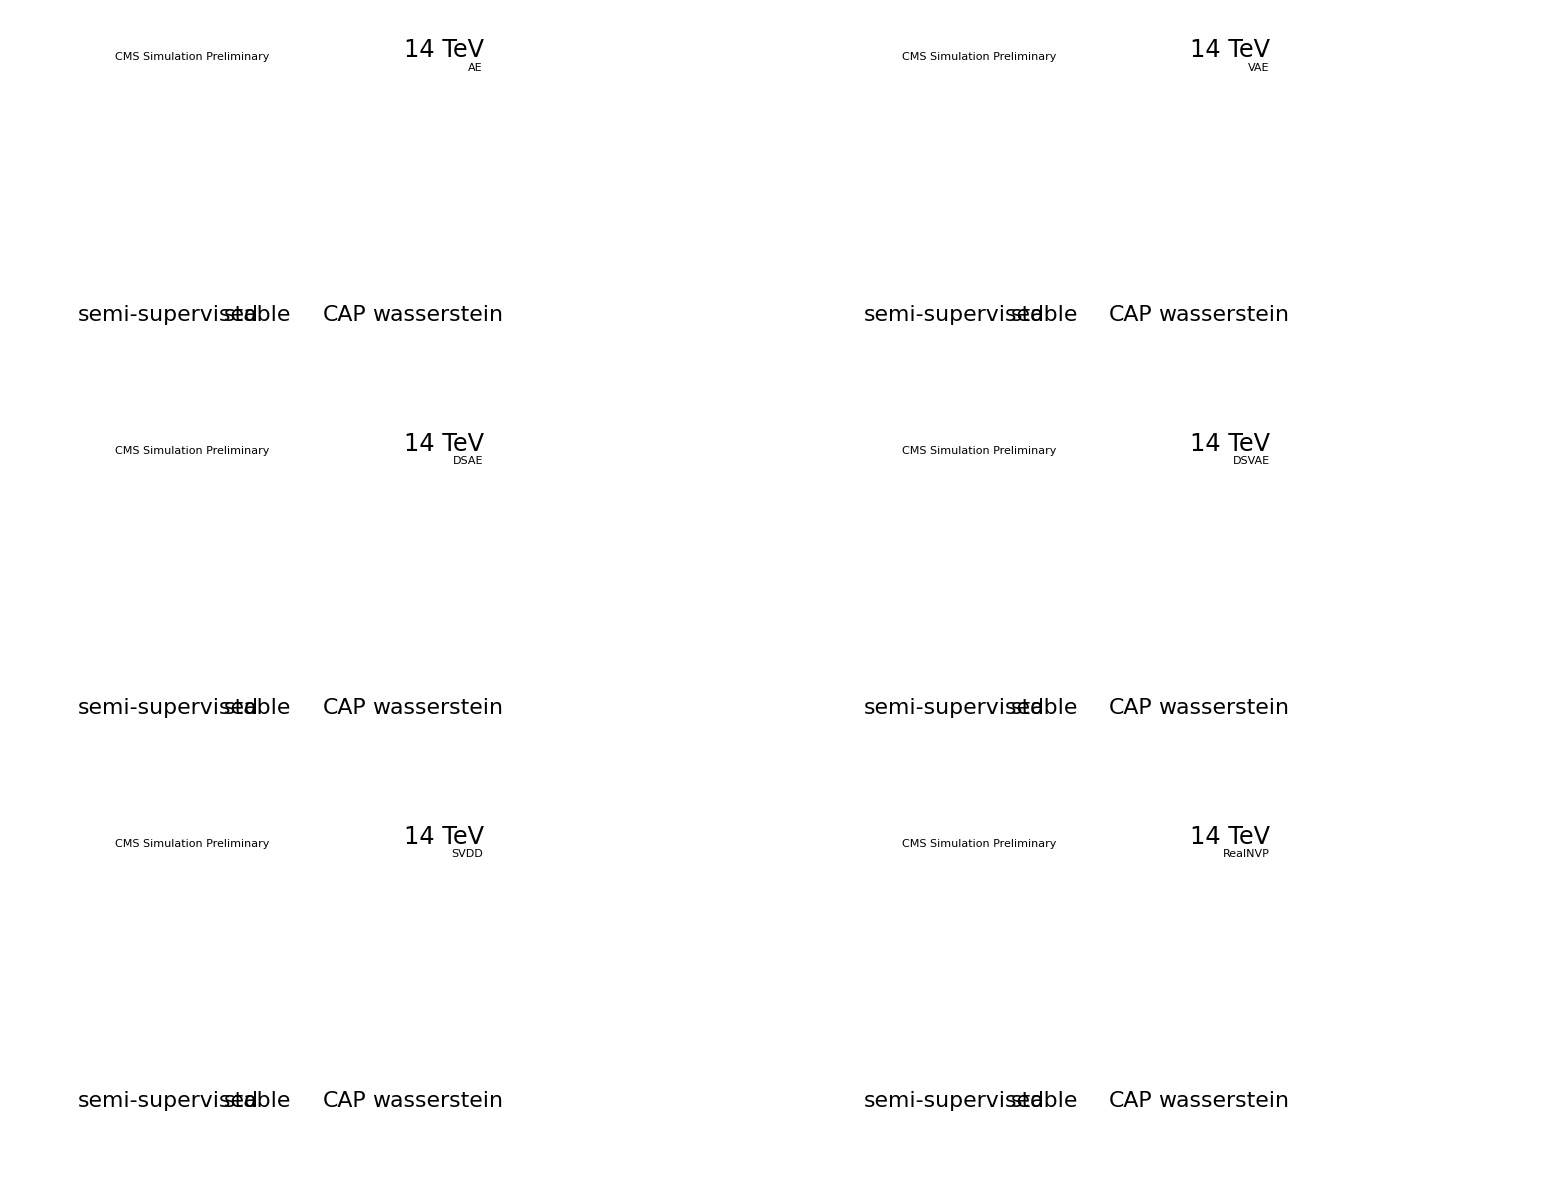

```mathematica
bestqGroups = rulePickArrays[rebuttalModelExps, bestQPick];
bestqPlot = makeRuleBoxGrid[dropEmptyModels[bestqGroups], 2]
Export[rebuttalOutDir <> "grouped_bestq" <> rebuttalTierSuffix <> ".svg", bestqPlot, "SVG"];
Export[rebuttalOutDir <> "grouped_bestq" <> rebuttalTierSuffix <> ".pdf", bestqPlot, "PDF"];
Export[rebuttalOutDir <> "grouped_bestq" <> rebuttalTierSuffix <> ".jpeg", bestqPlot, "JPEG"];
```

```mathematica
(* Quantile comparison for the Best Q' rule: the rule applied independently
   to the 250 Hz and q99 campaigns (disjoint trial sets from their own
   searches); test-split arrays at each run's own strategy checkpoint on both
   sides. Holm family per operating point, as in the legacy axis. *)
bestqGroups = rulePickArrays[rebuttalModelExps, bestQPick];
bestqGroupsQ99 = rulePickArrays[rebuttalModelExpsQ99, bestQPick];
printTable[QuantileAxisLatex[toLegacyGroups[bestqGroups],
   toLegacyGroups[bestqGroupsQ99]]];
printTable[QuantileAxisMarkdown[toLegacyGroups[bestqGroups],
   toLegacyGroups[bestqGroupsQ99]]];
```

note: no harvest CSV for physics_dte_q99_pareto -- omitting this model.

\begin{tabular}{lcccccccc}
\toprule
 & \multicolumn{4}{c}{$q \approx 0.999991$ (250\,Hz)} & \multicolumn{4}{c}{$q = 0.99$} \\
Arch. & $\Delta_{\mathrm{C-S}}$ & $p$ & $\Delta_{\mathrm{C-W}}$ & $p$ & $\Delta_{\mathrm{C-S}}$ & $p$ & $\Delta_{\mathrm{C-W}}$ & $p$ \\
\midrule
AE & 2.44 & 0.002$^{*}$ & 2.98 & <0.001$^{*}$ & -6.23 & <0.001$^{*}$ & -11.42 & <0.001$^{*}$ \\
VAE & 0.96 & 0.050 & 0.01 & 1.000 & 8.87 & <0.001$^{*}$ & 8.80 & <0.001$^{*}$ \\
DSAE & 3.02 & 0.002$^{*}$ & 3.82 & 0.062 & -2.67 & <0.001$^{*}$ & -4.01 & <0.001$^{*}$ \\
DSVAE & 3.28 & <0.001$^{*}$ & 2.36 & 0.062 & 0.52 & 0.368 & 2.40 & 0.342 \\
SVDD & 0.82 & 0.359 & -5.70 & <0.001$^{*}$ & -23.84 & <0.001$^{*}$ & n/a & n/a \\
RealNVP & 0.01 & 1.000 & 0.31 & 1.000 & 0.84 & 0.342 & 5.30 & <0.001$^{*}$ \\
\bottomrule
\end{tabular}

| Arch. | d(C-S) tail | p | d(C-W) tail | p | d(C-S) q99 | p | d(C-W) q99 | p |
|---|---|---|---|---|---|---|---|---|
| AE | 2.44 | 0.002* | 2.98 | <0.001* | -6.23 | <0.001* | -11.42 | <0.001* |
| VAE | 0.96 | 0.050 | 0.01 | 1.000 | 8.87 | <0.001* | 8.80 | <0.001* |
| DSAE | 3.02 | 0.002* | 3.82 | 0.062 | -2.67 | <0.001* | -4.01 | <0.001* |
| DSVAE | 3.28 | <0.001* | 2.36 | 0.062 | 0.52 | 0.368 | 2.40 | 0.342 |
| SVDD | 0.82 | 0.359 | -5.70 | <0.001* | -23.84 | <0.001* | n/a | n/a |
| RealNVP | 0.01 | 1.000 | 0.31 | 1.000 | 0.84 | 0.342 | 5.30 | <0.001* |

## Pareto Knee Selection

```mathematica
kneeGroups = rulePickArrays[rebuttalModelExps, kneePick];
kneeTabRows = HolmAdjustRows[BuildArchitectureRowsCompactCollapse[toLegacyGroups[kneeGroups], 10000, 0.05]];
printTable[LatexTableFromRows[kneeTabRows, 2]];
printTable[MarkdownTableFromRows[kneeTabRows, 2]];
```

\begin{tabular}{lcccccccc}
\toprule
Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\
\midrule
AE & 3.99 & 3.53 & no-pick & 3.30 & n/a & n/a & $0.23^{+0.22}_{-0.19}$ & 0.200 \\
VAE & 4.77 & 4.70 & 4.62 & 4.55 & $0.07^{+0.40}_{-0.39}$ & 1.000 & $0.15^{+0.67}_{-0.73}$ & 1.000 \\
DSAE & 7.32 & 7.30 & no-pick & 4.15 & n/a & n/a & $3.14^{+2.51}_{-2.12}$ & 0.107 \\
DSVAE & 5.16 & 0.02 & no-pick & no-pick & n/a & n/a & n/a & n/a \\
SVDD & coll & 3.82 & 0.06 & no-pick & $3.75^{+2.38}_{-2.00}$ & <0.001 & n/a & n/a \\
RealNVP & 3.92 & 2.25 & 3.33 & 1.77 & $-1.08^{+0.59}_{-0.64}$ & <0.001 & $0.49^{+0.37}_{-0.35}$ & 0.041 \\
\bottomrule
\end{tabular}
% legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

| Arch. | Semi | CAP | Stable | W1 | CAP-Stable | p | CAP-W1 | p |
|---|---|---|---|---|---|---|---|---|
| AE | 3.99 | 3.53 | no-pick | 3.30 | n/a | n/a | $0.23^{+0.22}_{-0.19}$ | 0.200 |
| VAE | 4.77 | 4.70 | 4.62 | 4.55 | $0.07^{+0.40}_{-0.39}$ | 1.000 | $0.15^{+0.67}_{-0.73}$ | 1.000 |
| DSAE | 7.32 | 7.30 | no-pick | 4.15 | n/a | n/a | $3.14^{+2.51}_{-2.12}$ | 0.107 |
| DSVAE | 5.16 | 0.02 | no-pick | no-pick | n/a | n/a | n/a | n/a |
| SVDD | coll | 3.82 | 0.06 | no-pick | $3.75^{+2.38}_{-2.00}$ | <0.001 | n/a | n/a |
| RealNVP | 3.92 | 2.25 | 3.33 | 1.77 | $-1.08^{+0.59}_{-0.64}$ | <0.001 | $0.49^{+0.37}_{-0.35}$ | 0.041 |

legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

```mathematica
kneeGroups = rulePickArrays[rebuttalModelExps, kneePick];
kneePlot = makeRuleBoxGrid[dropEmptyModels[kneeGroups], 2]
Export[rebuttalOutDir <> "grouped_knee" <> rebuttalTierSuffix <> ".svg", kneePlot, "SVG"];
Export[rebuttalOutDir <> "grouped_knee" <> rebuttalTierSuffix <> ".pdf", kneePlot, "PDF"];
Export[rebuttalOutDir <> "grouped_knee" <> rebuttalTierSuffix <> ".jpeg", kneePlot, "JPEG"];
```

-Graphics-

```mathematica
(* Quantile comparison for the knee rule, same construction as the Best Q'
   axis: test-split arrays at each run's own strategy checkpoint on both
   sides; Holm family per operating point. *)
kneeGroups = rulePickArrays[rebuttalModelExps, kneePick];
kneeGroupsQ99 = rulePickArrays[rebuttalModelExpsQ99, kneePick];
printTable[QuantileAxisLatex[toLegacyGroups[kneeGroups],
   toLegacyGroups[kneeGroupsQ99]]];
printTable[QuantileAxisMarkdown[toLegacyGroups[kneeGroups],
   toLegacyGroups[kneeGroupsQ99]]];
```

\begin{tabular}{lcccccccc}
\toprule
 & \multicolumn{4}{c}{$q \approx 0.999991$ (250\,Hz)} & \multicolumn{4}{c}{$q = 0.99$} \\
Arch. & $\Delta_{\mathrm{C-S}}$ & $p$ & $\Delta_{\mathrm{C-W}}$ & $p$ & $\Delta_{\mathrm{C-S}}$ & $p$ & $\Delta_{\mathrm{C-W}}$ & $p$ \\
\midrule
AE & n/a & n/a & 0.23 & 0.200 & 1.33 & <0.001$^{*}$ & -0.57 & 0.756 \\
VAE & 0.07 & 1.000 & 0.15 & 1.000 & 7.16 & <0.001$^{*}$ & 6.62 & <0.001$^{*}$ \\
DSAE & n/a & n/a & 3.14 & 0.107 & -2.84 & <0.001$^{*}$ & -1.59 & 0.002$^{*}$ \\
DSVAE & n/a & n/a & n/a & n/a & 11.23 & 0.002$^{*}$ & 1.96 & 0.038$^{*}$ \\
SVDD & 3.75 & <0.001$^{*}$ & n/a & n/a & -4.52 & <0.001$^{*}$ & n/a & n/a \\
RealNVP & -1.08 & <0.001$^{*}$ & 0.49 & 0.041$^{*}$ & n/a & n/a & n/a & n/a \\
\bottomrule
\end{tabular}

| Arch. | d(C-S) tail | p | d(C-W) tail | p | d(C-S) q99 | p | d(C-W) q99 | p |
|---|---|---|---|---|---|---|---|---|
| AE | n/a | n/a | 0.23 | 0.200 | 1.33 | <0.001* | -0.57 | 0.756 |
| VAE | 0.07 | 1.000 | 0.15 | 1.000 | 7.16 | <0.001* | 6.62 | <0.001* |
| DSAE | n/a | n/a | 3.14 | 0.107 | -2.84 | <0.001* | -1.59 | 0.002* |
| DSVAE | n/a | n/a | n/a | n/a | 11.23 | 0.002* | 1.96 | 0.038* |
| SVDD | 3.75 | <0.001* | n/a | n/a | -4.52 | <0.001* | n/a | n/a |
| RealNVP | -1.08 | <0.001* | 0.49 | 0.041* | n/a | n/a | n/a | n/a |

## Spearman Ranking

```mathematica
printTable[spearmanMatrixLatex[rebuttalModelExps]];
printTable[spearmanMatrixMarkdown[rebuttalModelExps]];
```

\begin{tabular}{lcccc}
\toprule
Arch. & Semi & CAP & Stable & W1 \\
\midrule
AE & 0.79 (7) & 0.70 (5) & n/a (2) & -0.22 (15) \\
VAE & 0.46 (13) & 0.59 (13) & -0.50 (3) & 0.65 (24) \\
DSAE & 0.60 (5) & 0.29 (7) & n/a (1) & 0.68 (13) \\
DSVAE & 0.15 (19) & 0.78 (14) & n/a (2) & n/a (1) \\
SVDD & 0.70 (10) & 0.08 (14) & -0.26 (4) & n/a (1) \\
RealNVP & -0.20 (9) & -0.19 (11) & 0.00 (4) & -0.20 (4) \\
DTE & no-pick & no-pick & no-pick & no-pick \\
\bottomrule
\end{tabular}

| Arch. | Semi | CAP | Stable | W1 |
|---|---|---|---|---|
| AE | 0.79 (7) | 0.70 (5) | n/a (2) | -0.22 (15) |
| VAE | 0.46 (13) | 0.59 (13) | -0.50 (3) | 0.65 (24) |
| DSAE | 0.60 (5) | 0.29 (7) | n/a (1) | 0.68 (13) |
| DSVAE | 0.15 (19) | 0.78 (14) | n/a (2) | n/a (1) |
| SVDD | 0.70 (10) | 0.08 (14) | -0.26 (4) | n/a (1) |
| RealNVP | -0.20 (9) | -0.19 (11) | 0.00 (4) | -0.20 (4) |
| DTE | no-pick | no-pick | no-pick | no-pick |